# Analyze Märklin track signal

## Get MM2 signal from track

### Load files

```mathematica
Directory[]
```

/home/cmaier/scad/Maerklin/analysis

```mathematica
Dimensions[raw=Import["MM2.78.run*.csv"]]
```

{2,1048578,3}

```mathematica
Take[#,4]&/@raw
```

{{{X,CH1,},{Second,Volt,},{-0.231344,-17.2,},{-0.231343,-17.2,}},{{X,CH1,},{Second,Volt,},{-0.232,-17.2,},{-0.231999,-17.2,}}}

### Convert into time series

```mathematica
Dimensions[timeseries=Most/@Drop[#,2]&/@raw]
```

{2,1048576,2}

#### Calculate time step

```mathematica
Dimensions[ListConvolve[{1,-1},First/@#]&/@timeseries]
```

{2,1048575}

```mathematica
GraphicsGrid[{ListPlot[ListConvolve[{1,-1},First/@#],Frame->True,PlotRange->All,FrameLabel->{"sample","time step [s]"},PlotLabel->"Difference of sample time stamps"]}&/@timeseries]
```

-Graphics-

```mathematica
{Min[#],Max[#]}&[ListConvolve[{1,-1},First/@#]]&/@timeseries
```

{{0.,1.×10^-6},{0.,1.×10^-6}}

```mathematica
Median[ListConvolve[{1,-1},First/@#]]&/@timeseries
timestep=Round[First[%],10^-9]
```

{5.×10^-7,6.×10^-7}

1/2000000

### Display

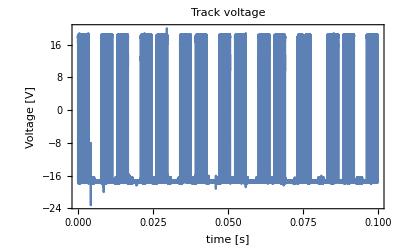

```mathematica
GraphicsGrid[{ListPlot[Select[#,0≤First[#]≤.1&],Frame->True,Joined->True,FrameLabel->{"time [s]","Voltage [V]"},PlotLabel->"Track voltage"]}&/@timeseries]
```

## Digitize time series

```mathematica
Dimensions[digitized=Map[{#⟦1⟧,HeavisideTheta[#⟦2⟧-0.0001]}&,timeseries,{2}]]
```

{2,1048576,2}

### Display

```mathematica
GraphicsGrid[{ListPlot[#,Frame->True,Joined->True,FrameLabel->{"time [s]",""},PlotLabel->"Digitized signal"]}&/@digitized]
```

-Graphics-

#### Runs of identical values for series

```mathematica
runs=SplitBy[#,Last]&/@digitized;
```

```mathematica
Length/@runs
```

{4137,3344}

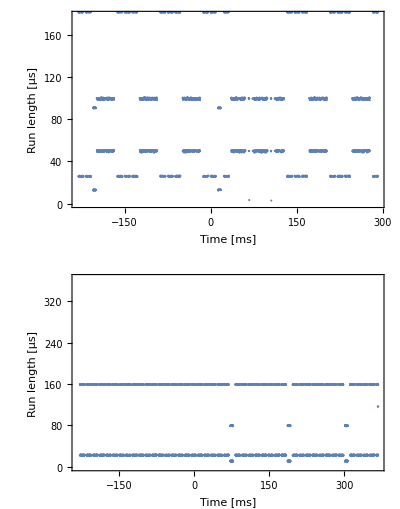

```mathematica
GraphicsGrid[{ListPlot[{10^3 First[First[#]],10^6 timestep Length[#]}&/@#,Frame->True,FrameLabel->{"Time [ms]","Run length [μs]"}]}&/@runs]
```

There are outliers in the MM2 packet sequence ... maybe a switch packet?

## Packets within the time series

### Short data packets

MM format, see 2.2.9 Einbettung von Steuerbefehlen im MM-Format

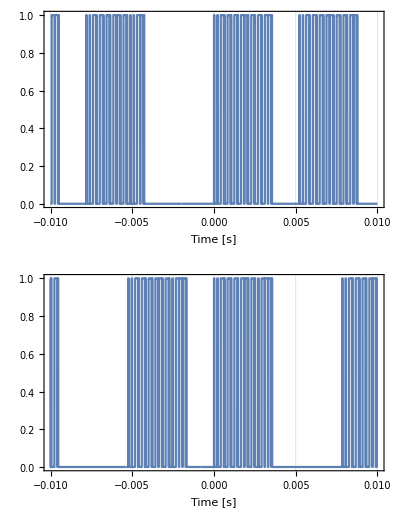

```mathematica
GraphicsGrid[{ListPlot[Select[#,-.01<First[#]<.01&],Frame->True,Joined->True,FrameLabel->{"Time [s]",""},GridLines->{Range[-.15,.15,1.*^-4],None}]}&/@digitized]
```

## Run length decoding

#### bit frame (100μs) per sampling step

```mathematica
timestep/10.^-4
```

0.005

#### Get run lengths of full traces

```mathematica
Length/@(fullruns=SplitBy[#,Last]&/@digitized)
```

{4137,3344}

### Run lengths in bit frames

```mathematica
rlbits=Map[timestep/10.^-4 Length[#]&,fullruns,{2}]
```

{{7.97,0.26,1.81,0.26,1.815,1.815,0.26,0.255,1.82,1.815,0.26,0.26,1.81,1.81,0.26,0.265,1.815,1.815,0.26,1.81,0.26,0.265,1.81,1.81,0.26,0.26,1.815,0.255,1.815,0.26,1.815,1.81,0.26,1.815,0.26,0.255,16.745,0.255,1.815,0.26,1.815,1.81,0.26,0.26,1.815,1.815,0.26,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.26,1.81,0.26,0.265,1.81,1.815,0.255,0.26,1.82,0.255,1.815,0.255,1.815,1.815,0.26,1.815,0.26,0.26,42.645,0.26,1.815,0.255,1.82,1.81,0.26,0.265,1.81,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.815,1.82,0.255,1.815,0.26,0.255,1.815,1.815,0.26,0.26,1.815,1.815,0.255,0.26,1.815,1.81,0.26,1.815,0.26,0.26,16.74,0.26,1.815,0.26,1.81,1.815,0.26,0.26,1.82,1.81,0.26,0.255,1.815,1.815,0.26,0.26,1.815,1.815,0.265,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.815,1.815,0.26,0.26,1.815,1.815,0.255,1.815,0.26,0.255,41.645,0.125,0.91,0.125,0.91,0.905,0.13,0.135,0.905,0.905,0.13,0.135,0.905,0.91,0.125,0.13,0.915,0.905,0.13,0.91,0.13,0.135,0.905,0.13,0.905,0.13,0.91,0.13,0.905,0.135,0.91,0.13,0.905,0.13,0.905,0.135,8.37,0.13,0.91,0.125,0.91,0.905,0.13,0.125,0.91,0.905,0.13,0.13,0.905,0.91,0.135,0.13,0.905,0.91,0.13,0.91,0.125,0.13,0.91,0.13,0.91,0.13,0.91,0.135,0.905,0.13,0.905,0.13,0.905,0.13,0.905,0.13,15.85,1.,0.505,0.995,0.995,0.5,0.995,0.505,0.49,0.99,0.99,0.99,0.99,0.985,0.99,0.99,1.,0.505,0.505,0.5,0.505,0.5,0.505,0.5,0.495,1.,0.5,0.495,0.995,0.505,0.49,0.99,0.985,1.,0.5,0.505,0.5,0.505,0.495,0.495,0.995,0.505,0.49,0.985,0.985,0.995,0.5,0.495,0.99,0.99,1.,0.505,0.495,0.505,0.495,1.,0.5,0.49,1.,0.5,0.495,0.99,0.995,0.5,0.5,0.505,0.49,0.985,0.99,1.,0.5,0.495,0.99,0.99,0.985,0.99,0.985,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.985,0.99,0.995,0.505,0.5,0.5,0.49,1.,0.5,0.495,0.985,0.995,0.5,0.5,0.505,0.49,1.005,0.5,0.5,1.,0.5,1.,1.005,0.5,1.005,1.,0.5,0.995,0.995,0.5,1.005,1.,0.505,0.995,0.995,0.505,1.,0.5,0.495,0.985,0.985,0.985,0.99,1.,0.5,0.495,1.,0.5,0.495,0.99,1.,0.505,0.5,0.5,0.49,0.99,0.99,0.985,0.99,0.985,0.985,0.985,1.005,0.5,0.5,0.5,0.505,0.5,0.495,0.99,0.99,0.99,0.985,0.99,0.995,0.98,0.99,0.985,0.99,0.985,1.,0.5,0.49,0.99,1.,0.5,0.5,0.505,0.5,0.505,0.49,1.,0.505,0.505,0.5,0.505,0.5,0.505,0.505,0.5,0.5,0.505,1.,0.505,1.,1.,0.505,1.,1.,0.5,0.995,0.995,0.5,0.985,14.955,1.,0.5,1.,1.,0.5,1.,0.5,0.495,0.99,0.99,0.99,0.995,1.,0.505,0.49,1.,0.505,0.49,0.99,1.005,0.5,0.505,0.5,0.49,0.99,0.99,0.99,0.99,0.985,0.99,0.985,0.995,0.5,0.5,0.505,0.505,0.5,0.495,0.99,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.985,0.985,0.985,0.995,0.5,0.49,0.99,1.,0.5,0.505,0.505,0.5,0.505,0.485,1.005,0.5,0.5,0.5,0.505,0.505,0.5,0.505,0.5,0.505,0.5,1.,0.5,1.,1.005,0.5,1.,0.995,0.505,1.,0.995,0.505,0.985,14.955,1.,0.505,0.995,0.995,0.505,1.,0.495,0.495,0.985,0.99,0.99,0.995,1.,0.5,0.495,1.,0.5,0.49,0.99,1.,0.5,0.505,0.5,0.495,0.99,0.985,0.985,0.985,0.985,0.99,0.99,1.,0.5,0.5,0.505,0.5,0.505,0.49,0.995,0.99,0.99,0.99,0.99,0.99,0.995,0.99,0.99,0.985,0.985,1.,0.505,0.49,0.99,0.995,0.495,0.505,0.495,0.5,0.505,0.495,0.995,0.505,0.5,0.5,0.505,0.505,0.5,0.505,0.5,0.505,0.5,1.,0.505,0.995,0.995,0.5,1.,1.,0.505,1.,1.,0.505,0.985,54.775,0.26,1.815,0.26,1.815,1.81,0.26,0.255,1.815,1.815,0.255,0.26,1.82,1.81,0.26,0.255,1.815,1.81,0.265,1.815,0.26,0.26,1.815,1.81,0.265,0.26,1.81,0.26,1.815,0.255,1.815,1.81,0.26,1.82,0.26,0.255,16.745,0.26,1.815,0.26,1.815,1.81,0.265,0.255,1.815,1.815,0.26,0.265,1.815,1.815,0.26,0.26,1.815,1.81,0.26,1.815,0.26,0.26,1.815,1.815,0.26,0.26,1.815,0.255,1.815,0.26,1.81,1.815,0.255,1.815,0.26,0.26,42.64,0.265,1.81,0.26,1.815,1.815,0.26,0.26,1.81,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.815,1.815,0.255,1.815,0.26,0.255,1.815,1.82,0.255,0.26,1.82,1.81,0.26,0.26,1.81,0.26,1.81,1.815,0.26,0.26,16.75,0.26,1.815,0.26,1.815,1.81,0.26,0.26,1.82,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.815,1.815,0.26,1.82,0.26,0.265,1.82,1.81,0.26,0.255,1.815,1.81,0.265,0.26,1.815,0.255,1.82,1.81,0.26,0.26,42.645,0.26,1.815,0.255,1.82,1.81,0.265,0.26,1.81,1.815,0.255,0.26,1.82,1.815,0.26,0.26,1.815,1.815,0.26,1.815,0.265,0.255,1.815,1.81,0.26,0.26,1.815,0.255,1.815,0.265,1.815,1.81,0.26,1.815,0.26,0.255,16.745,0.255,1.815,0.26,1.815,1.815,0.265,0.26,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.82,1.81,0.265,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.815,0.255,1.815,0.26,1.81,1.82,0.255,1.815,0.26,0.255,41.65,1.,0.505,1.,1.,0.505,1.,0.5,0.49,0.99,0.985,0.985,0.985,0.99,0.99,0.99,0.995,0.505,0.5,0.505,0.495,0.505,0.505,0.5,0.495,1.,0.505,0.49,1.,0.505,0.49,0.985,0.995,1.,0.5,0.5,0.505,0.5,0.505,0.485,1.,0.5,0.495,0.99,0.985,1.,0.5,0.485,0.99,0.99,1.,0.5,0.5,0.505,0.495,1.,0.5,0.495,1.,0.505,0.49,0.985,0.995,0.5,0.505,0.5,0.49,0.985,0.985,0.995,0.5,0.495,0.99,0.99,0.99,0.985,0.995,0.99,0.985,0.985,0.985,0.985,0.99,0.99,0.99,0.99,1.005,0.5,0.505,0.5,0.495,1.,0.505,0.49,0.99,0.995,0.505,0.505,0.5,0.49,1.,0.505,0.5,1.,0.5,1.,1.,0.505,1.,0.995,0.505,0.995,1.,0.5,1.01,1.,0.5,1.,1.005,0.5,0.995,0.5,0.495,0.99,0.985,0.995,0.99,1.,0.5,0.49,1.,0.505,0.49,0.985,1.,0.495,0.505,0.505,0.49,0.985,0.99,0.99,0.99,0.99,0.985,0.99,1.005,0.5,0.505,0.5,0.505,0.5,0.49,0.99,0.99,0.99,0.99,0.99,0.985,0.99,0.99,0.985,0.985,0.99,1.,0.5,0.49,0.99,0.995,0.505,0.5,0.505,0.505,0.5,0.495,1.,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.505,0.5,0.5,1.005,0.5,1.005,0.995,0.505,0.995,0.995,0.5,0.995,1.,0.505,0.98,14.95,1.,0.5,1.,1.,0.5,1.,0.505,0.49,0.99,0.99,0.99,0.99,1.,0.505,0.49,1.005,0.5,0.49,0.995,1.,0.5,0.5,0.505,0.49,0.99,0.99,0.985,0.99,0.99,0.99,0.985,1.,0.505,0.495,0.505,0.505,0.5,0.49,0.985,0.99,0.99,0.985,0.985,0.99,0.995,0.99,0.99,0.985,0.985,1.,0.505,0.49,0.99,0.995,0.5,0.505,0.5,0.5,0.5,0.49,0.995,0.505,0.495,0.5,0.505,0.5,0.505,0.505,0.5,0.505,0.5,1.,0.5,0.995,1.005,0.5,1.,1.,0.5,1.,1.,0.505,0.985,14.95,1.,0.505,1.,1.,0.495,1.,0.505,0.485,0.99,0.99,0.985,0.985,1.,0.505,0.485,1.,0.495,0.495,0.99,0.995,0.505,0.5,0.505,0.49,0.985,0.995,0.985,0.985,0.99,0.99,0.99,1.005,0.5,0.505,0.5,0.505,0.5,0.495,0.99,0.99,0.985,0.99,0.995,0.99,0.99,0.985,0.985,0.99,0.99,1.,0.5,0.495,0.99,0.995,0.5,0.5,0.5,0.5,0.505,0.49,1.,0.5,0.5,0.5,0.5,0.505,0.5,0.5,0.5,0.505,0.5,1.005,0.5,1.,1.,0.505,0.995,1.,0.5,1.,0.995,0.505,0.98,54.775,0.26,1.815,0.265,1.815,1.81,0.26,0.255,1.815,1.81,0.265,0.26,1.815,1.815,0.265,0.26,1.815,1.81,0.26,1.81,0.26,0.26,1.815,0.255,1.815,0.26,1.81,0.26,1.82,0.26,1.81,1.815,0.265,1.81,0.26,0.265,16.745,0.26,1.815,0.26,1.81,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.815,1.815,0.255,0.26,1.815,1.815,0.26,1.815,0.26,0.26,1.815,0.255,1.815,0.26,1.81,0.26,1.81,0.265,1.815,1.81,0.26,1.81,0.26,0.26,42.635,0.26,1.81,0.265,1.815,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.815,1.81,0.265,0.26,1.815,1.815,0.265,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.815,0.255,1.815,0.26,1.81,1.82,0.255,1.815,0.26,0.255,16.745,0.26,1.815,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.265,0.255,1.815,1.815,0.26,0.265,1.815,1.81,0.265,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.81,0.26,1.82,0.255,1.815,1.815,0.26,1.81,0.26,0.26,42.64,0.26,1.815,0.26,1.81,1.815,0.26,0.255,1.82,1.81,0.26,0.255,1.815,1.81,0.26,0.26,1.815,1.815,0.265,1.81,0.265,0.255,1.815,0.26,1.815,0.26,1.82,1.815,0.26,0.255,1.82,1.81,0.265,1.81,0.26,0.265,16.745,0.26,1.815,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.265,0.255,1.815,1.81,0.265,0.265,1.81,1.815,0.26,1.815,0.26,0.255,1.815,0.265,1.81,0.26,1.815,1.815,0.26,0.255,1.815,1.81,0.265,1.81,0.26,0.265,41.645,1.,0.5,1.,1.005,0.5,0.995,0.5,0.495,0.99,0.99,0.985,0.99,0.985,0.99,0.99,0.995,0.505,0.5,0.505,0.5,0.5,0.505,0.5,0.495,1.,0.5,0.49,0.995,0.505,0.485,0.99,0.99,0.995,0.5,0.5,0.5,0.505,0.505,0.49,1.,0.505,0.49,0.995,0.99,0.995,0.5,0.49,0.99,0.99,1.005,0.5,0.505,0.5,0.49,1.,0.5,0.485,1.,0.505,0.49,0.985,1.,0.5,0.505,0.5,0.49,0.985,0.99,0.995,0.5,0.495,0.99,0.99,0.985,0.99,0.995,0.99,0.99,0.985,0.985,0.99,0.99,0.985,0.985,0.99,0.995,0.505,0.5,0.505,0.485,0.995,0.5,0.495,0.99,0.995,0.505,0.5,0.505,0.49,1.,0.5,0.505,1.,0.5,1.,1.005,0.5,1.,1.,0.505,1.,1.,0.505,1.01,1.,0.505,0.995,1.,0.495,1.,0.5,0.49,0.99,0.99,0.985,0.99,1.,0.505,0.49,1.,0.5,0.495,0.99,1.,0.495,0.505,0.5,0.495,0.985,0.99,0.99,0.99,0.99,0.99,0.985,1.,0.5,0.505,0.505,0.5,0.505,0.49,0.985,0.995,0.99,0.985,0.985,0.985,0.985,0.985,0.995,0.99,0.99,1.,0.505,0.49,0.99,1.,0.505,0.5,0.5,0.505,0.5,0.495,1.,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.5,0.505,1.,0.495,1.005,1.,0.5,0.995,1.,0.5,1.005,1.,0.5,0.98,14.96,1.,0.505,0.995,1.,0.495,1.,0.505,0.49,0.985,0.995,0.985,0.99,1.,0.505,0.49,1.,0.5,0.495,0.99,0.995,0.505,0.5,0.5,0.49,0.99,0.995,0.985,0.99,0.99,0.985,0.985,1.,0.5,0.5,0.5,0.505,0.5,0.495,0.985,0.99,0.99,0.99,0.985,0.99,0.99,0.995,0.985,0.99,0.985,0.995,0.5,0.49,0.99,1.,0.5,0.5,0.5,0.5,0.5,0.495,1.,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.505,0.5,0.505,1.,0.5,0.995,0.995,0.5,1.,1.,0.5,1.,1.,0.505,0.98,14.95,1.,0.5,1.,1.,0.5,1.,0.5,0.495,0.99,0.99,0.985,0.985,1.,0.505,0.49,1.,0.5,0.495,0.985,0.995,0.5,0.5,0.505,0.49,0.985,0.995,0.985,0.99,0.99,0.99,0.99,0.995,0.5,0.505,0.5,0.505,0.5,0.495,0.985,0.99,0.99,0.99,0.99,0.99,0.99,0.995,0.99,0.99,0.99,0.995,0.505,0.49,0.985,0.995,0.5,0.505,0.5,0.505,0.5,0.495,0.995,0.5,0.5,0.5,0.5,0.505,0.5,0.505,0.505,0.5,0.5,1.005,0.495,0.995,1.,0.5,1.,0.995,0.505,1.,0.995,0.5,0.98,54.775,0.255,1.815,0.26,1.81,1.81,0.26,0.26,1.815,1.815,0.26,0.265,1.81,1.81,0.26,0.26,1.815,1.815,0.26,1.81,0.26,0.26,1.815,1.81,0.26,0.26,1.815,0.26,1.815,0.26,1.815,1.81,0.26,1.815,0.255,0.26,16.74,0.26,1.81,0.26,1.81,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.81,1.81,0.26,0.26,1.82,1.815,0.26,1.81,0.26,0.26,1.815,1.81,0.265,0.26,1.815,0.26,1.815,0.26,1.81,1.815,0.265,1.815,0.265,0.265,42.645,0.26,1.81,0.26,1.81,1.815,0.26,0.265,1.81,1.81,0.26,0.26,1.815,1.81,0.265,0.26,1.815,1.81,0.26,1.815,0.255,0.26,1.815,1.815,0.265,0.26,1.81,1.815,0.255,0.26,1.815,1.815,0.26,1.81,0.26,0.26,16.745,0.255,1.815,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.255,1.815,1.81,0.265,0.26,1.815,1.815,0.255,1.815,0.26,0.26,1.815,1.815,0.265,0.26,1.815,1.815,0.255,0.26,1.82,1.81,0.26,1.81,0.26,0.26,41.645,0.13,0.905,0.13,0.91,0.905,0.13,0.125,0.91,0.905,0.13,0.13,0.905,0.905,0.135,0.135,0.905,0.905,0.13,0.905,0.135,0.13,0.91,0.13,0.91,0.13,0.905,0.13,0.905,0.13,0.91,0.13,0.91,0.13,0.905,0.13,8.37,0.135,0.905,0.13,0.905,0.905,0.13,0.13,0.905,0.905,0.13,0.13,0.905,0.91,0.135,0.13,0.91,0.905,0.13,0.905,0.13,0.135,0.905,0.135,0.905,0.13,0.905,0.13,0.91,0.13,0.905,0.135,0.91,0.13,0.905,0.13,55.675,0.26,1.815,0.26,1.815,1.815,0.26,0.265,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.82,1.815,0.265,1.815,0.26,0.26,1.81,1.815,0.26,0.255,1.815,0.26,1.815,0.26,1.82,1.81,0.26,1.81,0.26,0.26,16.745,0.26,1.815,0.26,1.81,1.815,0.26,0.255,1.815,1.81,0.26,0.26,1.82,1.815,0.26,0.26,1.815,1.81,0.26,1.82,0.26,0.26,1.81,1.815,0.26,0.255,1.815,0.26,1.815,0.265,1.815,1.815,0.255,1.815,0.26,0.265,41.645,0.995,0.505,1.,1.005,0.5,1.,0.5,0.49,0.99,0.99,0.99,0.99,0.985,0.99,0.985,1.,0.505,0.5,0.5,0.505,0.5,0.5,0.5,0.495,0.995,0.505,0.49,1.,0.505,0.49,0.985,0.99,0.995,0.5,0.505,0.505,0.5,0.505,0.49,0.995,0.5,0.49,0.985,0.99,0.995,0.505,0.49,0.99,0.99,1.,0.5,0.505,0.5,0.49,0.995,0.505,0.485,0.995,0.505,0.495,0.99,0.995,0.5,0.505,0.5,0.49,0.985,0.985,1.,0.5,0.49,0.99,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.99,0.985,0.995,0.985,0.99,0.985,1.,0.505,0.505,0.5,0.495,1.,0.495,0.495,0.985,0.995,0.505,0.495,0.5,0.495,1.,0.5,0.505,1.,0.5,1.,1.,0.5,1.,1.,0.505,1.,1.,0.505,1.01,1.,0.505,1.,1.,0.5,1.,0.5,0.495,0.99,0.99,0.99,0.99,0.99,0.99,0.985,1.,0.5,0.505,0.5,0.505,0.505,0.49,0.995,0.505,0.49,0.99,0.985,0.985,0.99,0.99,0.985,1.,0.5,0.5,0.5,0.505,0.5,0.505,0.505,0.5,0.505,0.5,0.5,0.5,0.505,0.505,0.5,0.495,0.995,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.495,0.995,0.505,0.5,0.5,0.495,0.505,0.505,0.5,0.5,0.505,0.5,0.495,0.5,0.5,0.505,0.505,0.485,1.,0.505,0.505,0.5,0.505,0.495,0.505,0.505,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.505,0.485,1.,0.5,0.495,0.995,0.505,0.49,0.995,0.505,0.5,0.505,0.495,0.99,0.995,1.,0.505,0.995,1.,0.505,1.,0.495,0.495,0.985,0.985,0.985,0.99,0.99,0.985,0.99,0.995,0.505,0.5,0.505,0.505,0.5,0.505,0.495,0.495,0.995,0.495,0.49,1.,0.505,0.49,0.99,0.99,1.,0.5,0.5,0.5,0.495,0.505,0.485,1.005,0.5,0.495,0.99,0.985,1.,0.5,0.49,0.99,0.99,1.,0.495,0.5,0.505,0.49,1.,0.5,0.49,1.005,0.5,0.495,0.99,1.,0.505,0.5,0.5,0.49,0.985,0.99,0.995,0.5,0.495,0.985,0.985,0.985,0.99,0.99,0.99,0.985,0.99,0.985,0.99,0.99,0.99,0.985,0.99,0.995,0.505,0.5,0.505,0.495,1.,0.5,0.485,0.99,0.995,0.505,0.5,0.5,0.49,1.005,0.5,0.505,0.995,0.5,1.005,1.,0.5,1.,0.995,0.5,1.,1.,0.505,1.,1.,1.,0.505,0.5,0.505,0.5,60.22,1.,0.5,1.,0.995,0.5,0.995,0.995,0.5,0.995,0.035,60.19,0.995,0.5,0.995,0.995,0.5,15.935,1.,0.5,1.,1.,0.495,0.995,0.505,0.485,0.995,0.99,0.985,0.99,0.995,0.505,0.49,1.,0.5,0.495,0.985,1.,0.505,0.5,0.5,0.485,0.99,0.99,0.985,0.99,0.99,0.99,0.985,1.,0.495,0.5,0.505,0.5,0.5,0.49,0.99,0.985,0.99,0.985,0.99,0.985,0.99,0.995,0.985,0.99,0.985,0.995,0.5,0.495,0.99,1.,0.505,0.495,0.505,0.5,0.5,0.495,1.,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.495,0.5,0.495,1.005,0.5,1.,0.995,0.5,0.995,0.995,0.505,1.,1.,0.5,0.985,14.95,1.,0.505,1.,1.,0.505,1.,0.5,0.49,0.99,0.985,0.985,0.99,0.985,0.99,0.99,1.,0.5,0.505,0.505,0.5,0.5,0.49,1.,0.505,0.495,0.985,0.99,0.985,0.985,0.985,0.985,1.005,0.495,0.505,0.5,0.505,0.5,0.5,0.5,0.5,0.505,0.5,0.505,0.5,0.5,0.505,0.5,0.495,0.995,0.505,0.5,0.505,0.5,0.505,0.505,0.5,0.495,0.5,0.505,0.5,0.5,0.5,0.5,0.505,0.485,0.995,0.5,0.5,0.5,0.505,0.495,0.505,0.5,0.5,0.505,0.5,0.505,0.505,0.5,0.5,0.5,0.495,0.995,0.505,0.5,0.505,0.5,0.505,0.5,0.5,0.5,0.5,0.505,0.5,0.505,0.505,0.5,0.5,0.49,1.,0.505,0.485,1.,0.5,0.485,1.,0.495,0.5,0.505,0.49,0.99,1.005,0.995,0.5,1.,1.,0.5,1.,0.495,0.495,0.99,0.99,0.99,0.99,0.985,0.99,0.99,0.995,0.505,0.5,0.505,0.505,0.495,0.505,0.5,0.49,0.995,0.505,0.49,1.,0.5,0.49,0.99,0.985,1.,0.505,0.495,0.505,0.5,0.505,0.495,1.,0.5,0.495,0.985,0.985,1.,0.505,0.49,0.99,0.995,1.,0.5,0.505,0.495,0.495,0.995,0.505,0.49,1.,0.5,0.495,0.985,1.,0.5,0.5,0.505,0.485,0.99,0.995,0.995,0.5,0.495,0.985,0.99,0.99,0.99,0.985,0.985,0.985,0.99,0.99,0.985,0.985,0.985,0.99,0.985,1.,0.495,0.505,0.495,0.495,0.995,0.505,0.485,0.985,1.005,0.5,0.505,0.5,0.49,1.,0.505,0.495,1.005,0.5,0.995,0.995,0.5,0.995,1.,0.505,0.995,1.,0.5,1.,1.,0.995,0.505,0.5,0.5,0.5,60.225,1.,0.495,0.995,0.995,0.5,0.995,0.995,0.5,0.995,0.03,60.2,0.995,0.5,0.995,0.995,0.5,15.94,1.,0.505,0.995,1.,0.495,1.,0.505,0.49,0.985,0.99,0.99,0.99,0.995,0.505,0.495,1.,0.495,0.49,0.99,0.995,0.5,0.5,0.505,0.495,0.985,0.985,0.99,0.995,0.985,0.99,0.99,1.,0.505,0.5,0.505,0.5,0.5,0.495,0.99,0.985,0.985,0.99,0.99,0.99,0.99,0.985,0.985,0.99,0.99,1.,0.5,0.495,0.99,1.,0.505,0.5,0.505,0.5,0.5,0.49,0.995,0.505,0.495,0.505,0.505,0.5,0.5,0.5,0.505,0.505,0.5,1.,0.505,1.,1.,0.505,1.,1.,0.5,1.005,1.,0.5,0.985,14.955,1.,0.5,1.,0.995,0.5,1.005,0.5,0.495,0.985,0.99,0.99,0.99,1.,0.5,0.49,1.,0.495,0.495,0.99,1.,0.5,0.5,0.505,0.485,0.985,0.985,0.99,0.99,0.985,0.99,0.99,1.,0.495,0.505,0.5,0.505,0.5,0.49,0.985,0.985,0.99,0.99,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.995,0.5,0.49,0.99,1.,0.5,0.505,0.5,0.505,0.5,0.49,0.995,0.505,0.5,0.505,0.495,0.5,0.505,0.5,0.505,0.495,0.5,1.,0.505,0.995,0.995,0.505,1.,1.,0.505,1.,1.,0.5,0.985,54.785,0.255,1.815,0.26,1.815,1.815,0.265,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.255,1.815,1.81,0.265,1.82,0.26,0.255,1.82,1.81,0.265,0.26,1.81,1.815,0.26,0.255,1.82,0.255,1.815,1.81,0.26,0.26,16.74,0.26,1.81,0.26,1.82,1.815,0.26,0.255,1.815,1.81,0.26,0.265,1.815,1.815,0.26,0.26,1.815,1.81,0.26,1.815,0.26,0.255,1.815,1.81,0.26,0.26,1.815,1.815,0.26,0.255,1.815,0.26,1.815,1.81,0.265,0.26,42.65,0.26,1.815,0.265,1.81,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.815,1.81,0.26,1.82,0.26,0.26,1.815,1.81,0.26,0.26,1.82,0.255,1.815,0.26,1.81,1.815,0.255,1.815,0.26,0.26,16.745,0.265,1.81,0.26,1.815,1.815,0.265,0.26,1.81,1.81,0.26,0.26,1.82,1.815,0.26,0.26,1.815,1.815,0.26,1.815,0.26,0.26,1.81,1.81,0.26,0.265,1.815,0.255,1.82,0.26,1.81,1.815,0.255,1.815,0.26,0.255,42.65,0.255,1.82,0.26,1.81,1.815,0.26,0.26,1.815,1.81,0.265,0.265,1.81,1.815,0.26,0.26,1.815,1.815,0.26,1.815,0.265,0.26,1.815,0.26,1.815,0.26,1.815,0.26,1.815,0.26,1.81,1.82,0.26,1.815,0.265,0.26,16.745,0.26,1.81,0.265,1.82,1.81,0.265,0.255,1.815,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.815,1.81,0.265,1.815,0.255,0.26,1.815,0.255,1.815,0.26,1.81,0.265,1.815,0.26,1.82,1.81,0.26,1.81,0.26,0.26,41.645,1.,0.505,1.,0.995,0.5,1.,0.5,0.49,0.985,0.985,0.985,0.99,0.99,0.985,0.985,1.,0.505,0.495,0.505,0.505,0.5,0.505,0.5,0.495,1.,0.505,0.49,1.,0.5,0.49,0.985,0.995,0.995,0.505,0.5,0.505,0.5,0.505,0.49,1.005,0.5,0.49,0.99,0.99,1.,0.5,0.49,0.99,0.985,1.,0.5,0.505,0.5,0.495,0.995,0.5,0.49,1.,0.505,0.495,0.985,1.,0.495,0.505,0.5,0.495,0.99,0.99,1.,0.5,0.495,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.985,0.99,0.99,0.985,0.99,0.99,0.985,1.,0.5,0.5,0.505,0.495,1.,0.5,0.495,0.99,1.,0.505,0.495,0.505,0.495,1.,0.5,0.505,1.,0.5,1.,1.,0.495,1.,0.995,0.495,1.,1.,0.5,1.01,1.,0.505,1.,1.,0.5,1.,0.505,0.495,0.985,0.99,0.99,0.99,1.005,0.5,0.49,1.,0.5,0.495,0.99,1.,0.505,0.505,0.5,0.495,0.99,0.99,0.99,0.99,0.99,0.99,0.99,0.995,0.505,0.5,0.505,0.495,0.505,0.49,0.99,0.99,0.985,0.99,0.99,0.985,0.99,0.995,0.985,0.99,0.985,1.,0.5,0.495,0.99,1.,0.5,0.5,0.505,0.5,0.505,0.49,1.005,0.5,0.505,0.5,0.5,0.5,0.5,0.505,0.5,0.5,0.5,1.,0.505,1.,1.,0.505,1.,1.,0.505,1.,1.,0.5,0.985,14.955,1.,0.5,1.,0.995,0.5,0.995,0.5,0.495,0.99,0.99,0.99,0.985,1.,0.505,0.49,1.005,0.5,0.495,0.99,1.,0.5,0.5,0.505,0.49,0.99,0.985,0.99,0.99,0.99,0.985,0.99,1.,0.5,0.5,0.5,0.505,0.5,0.495,0.985,0.99,0.99,0.995,0.99,0.99,0.99,0.99,0.99,0.99,0.985,1.,0.5,0.495,0.99,0.995,0.505,0.5,0.505,0.5,0.5,0.49,1.,0.5,0.505,0.5,0.505,0.505,0.5,0.505,0.5,0.505,0.495,1.,0.5,1.,1.,0.505,0.995,1.,0.495,1.005,1.,0.5,0.99,14.95,1.005,0.505,1.,1.,0.495,1.,0.505,0.49,0.985,0.99,0.995,0.99,0.995,0.495,0.495,1.,0.505,0.495,0.985,1.,0.495,0.505,0.5,0.495,0.99,0.985,0.99,0.99,0.995,0.99,0.99,1.,0.5,0.5,0.505,0.5,0.5,0.49,0.985,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.995,0.99,0.99,0.995,0.505,0.49,0.985,1.,0.5,0.5,0.5,0.505,0.5,0.49,0.995,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.505,0.5,1.005,0.495,0.995,1.005,0.5,1.,1.,0.5,0.995,0.995,0.5,0.98,54.78,0.26,1.81,0.26,1.815,1.81,0.26,0.265,1.81,1.815,0.26,0.255,1.82,1.81,0.26,0.26,1.815,1.815,0.26,1.81,0.265,0.26,1.81,1.81,0.26,0.26,1.81,0.26,1.815,0.26,1.815,1.81,0.26,1.815,0.26,0.255,16.745,0.26,1.815,0.26,1.815,1.81,0.26,0.26,1.815,1.815,0.255,0.26,1.82,1.81,0.26,0.26,1.81,1.815,0.26,1.815,0.26,0.255,1.815,1.81,0.26,0.26,1.815,0.265,1.815,0.255,1.82,1.81,0.265,1.815,0.26,0.26,42.645,0.255,1.82,0.26,1.81,1.81,0.26,0.26,1.815,1.81,0.26,0.255,1.815,1.815,0.26,0.26,1.82,1.81,0.265,1.81,0.26,0.255,1.815,0.26,1.815,0.26,1.815,1.81,0.265,0.255,1.815,1.81,0.265,1.815,0.255,0.26,16.75,0.26,1.81,0.265,1.81,1.815,0.26,0.255,1.815,1.815,0.26,0.26,1.81,1.815,0.26,0.255,1.82,1.81,0.26,1.815,0.26,0.26,1.815,0.26,1.815,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.265,1.81,0.26,0.255,42.65,0.265,1.81,0.26,1.82,1.81,0.26,0.255,1.815,1.815,0.26,0.26,1.815,1.815,0.265,0.26,1.815,1.815,0.26,1.815,0.255,0.26,1.82,1.81,0.26,0.265,1.81,0.26,1.815,0.26,1.81,1.815,0.26,1.815,0.26,0.26,16.74,0.265,1.81,0.265,1.81,1.815,0.26,0.255,1.82,1.81,0.265,0.26,1.815,1.815,0.26,0.26,1.815,1.81,0.26,1.81,0.26,0.265,1.81,1.815,0.26,0.26,1.81,0.26,1.815,0.26,1.815,1.81,0.265,1.815,0.255,0.26,41.655,1.,0.5,0.99,1.,0.5,1.,0.5,0.495,0.985,0.985,0.99,0.99,0.99,0.99,0.985,0.995,0.505,0.5,0.505,0.5,0.5,0.5,0.5,0.495,1.,0.5,0.49,1.,0.5,0.49,0.99,0.99,1.,0.5,0.5,0.5,0.5,0.505,0.49,1.,0.5,0.49,0.985,0.99,1.,0.505,0.49,0.99,0.99,1.,0.505,0.505,0.5,0.495,1.,0.5,0.49,1.,0.505,0.49,0.99,1.005,0.5,0.505,0.5,0.495,0.985,0.99,1.,0.5,0.495,0.985,0.99,0.99,0.985,0.99,0.985,0.99,0.99,0.99,0.985,0.995,0.99,0.985,0.985,0.995,0.5,0.505,0.5,0.49,1.,0.5,0.49,0.99,1.,0.5,0.5,0.505,0.495,1.,0.495,0.5,1.,0.505,0.995,0.995,0.505,1.,1.,0.505,1.,1.,0.5,1.01,1.,0.5,1.,0.995,0.505,1.,0.5,0.495,0.99,0.99,0.99,0.99,1.,0.505,0.495,1.,0.5,0.49,0.99,0.995,0.505,0.5,0.505,0.495,0.985,0.985,0.985,0.99,0.985,0.99,0.99,1.,0.5,0.505,0.5,0.5,0.505,0.49,0.99,0.995,0.99,0.99,0.99,0.99,0.99,0.99,0.985,0.99,0.99,1.,0.5,0.495,0.99,1.,0.5,0.5,0.5,0.5,0.495,0.495,1.,0.505,0.5,0.5,0.495,0.505,0.5,0.505,0.5,0.5,0.505,1.,0.495,0.995,1.,0.5,1.,1.005,0.5,1.005,1.,0.5,0.985,14.955,1.005,0.5,0.995,1.,0.495,0.995,0.505,0.49,0.99,0.99,0.985,0.985,1.,0.505,0.485,1.,0.495,0.495,0.99,0.995,0.505,0.5,0.505,0.49,0.99,0.99,0.985,0.985,0.99,0.99,0.985,0.995,0.5,0.5,0.505,0.495,0.505,0.485,0.99,0.99,0.985,0.99,0.99,0.99,0.985,0.99,0.99,0.985,0.99,0.995,0.5,0.49,0.99,1.,0.5,0.505,0.5,0.505,0.5,0.495,1.,0.505,0.5,0.505,0.505,0.5,0.5,0.505,0.505,0.5,0.505,1.,0.5,1.,0.995,0.5,1.,1.,0.5,1.,1.,0.505,0.98,14.955,1.,0.505,0.995,0.995,0.505,1.,0.5,0.495,0.985,0.99,0.99,0.99,1.,0.5,0.49,1.,0.505,0.485,0.99,1.,0.5,0.505,0.5,0.495,0.99,0.99,0.985,0.995,0.99,0.99,0.99,0.995,0.505,0.505,0.5,0.5,0.5,0.495,0.99,0.985,0.985,0.995,0.99,0.985,0.99,0.985,0.99,0.99,0.99,0.995,0.505,0.49,0.995,1.,0.505,0.5,0.505,0.5,0.505,0.495,0.995,0.505,0.505,0.505,0.5,0.5,0.505,0.505,0.5,0.505,0.5,1.005,0.5,1.005,1.,0.5,1.,1.005,0.5,1.,1.,0.505,0.98,54.795,0.255,1.815,0.26,1.81,1.82,0.26,0.26,1.815,1.815,0.26,0.26,1.81,1.815,0.26,0.26,1.81,1.81,0.26,1.815,0.26,0.26,1.815,1.815,0.26,0.26,1.815,1.815,0.26,0.255,1.815,1.81,0.265,1.815,0.26,0.26,16.74,0.26,1.815,0.26,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.255,1.815,1.815,0.26,0.26,1.815,1.815,0.265,1.81,0.26,0.265,1.815,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.81,1.815,0.26,1.81,0.26,0.26,13.24},{37.025,0.225,1.59,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.23,1.59,0.23,1.595,0.23,1.59,0.23,1.585,0.23,0.225,1.595,0.23,1.585,1.595,0.23,1.59,0.23,0.23,14.685,0.23,1.59,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,1.59,0.225,1.59,0.23,1.59,0.23,1.59,0.225,0.225,1.595,0.23,1.595,1.59,0.23,1.59,0.23,0.23,37.4,0.23,1.59,0.225,1.59,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,0.235,1.585,1.59,0.23,1.59,0.225,1.59,0.23,0.23,14.685,0.225,1.595,0.23,1.59,1.595,0.23,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.585,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.23,1.59,0.23,1.59,1.59,0.225,1.59,0.225,1.59,0.23,0.225,37.395,0.23,1.59,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.595,0.23,1.59,0.23,1.585,0.23,1.585,0.23,1.595,0.225,0.225,1.59,0.23,1.59,1.59,0.23,1.59,0.225,0.225,14.685,0.23,1.585,0.23,1.595,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.23,1.59,0.23,1.59,0.225,1.59,0.23,0.225,1.59,0.23,1.595,1.595,0.23,1.59,0.23,0.23,37.405,0.225,1.59,0.225,1.59,1.59,0.23,0.225,1.59,1.595,0.23,0.23,1.59,1.595,0.23,0.23,1.59,1.585,0.23,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.595,0.23,1.59,1.595,0.225,1.59,0.23,1.59,0.225,0.23,14.68,0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.585,0.23,1.595,1.59,0.23,1.59,0.225,1.59,0.235,0.23,37.4,0.23,1.59,0.23,1.595,1.585,0.235,0.225,1.59,1.595,0.225,0.225,1.59,1.59,0.225,0.23,1.595,1.585,0.23,1.59,0.23,1.59,0.225,1.59,0.23,1.59,0.225,0.23,1.595,0.225,1.59,1.595,0.225,1.595,0.23,0.23,14.68,0.225,1.595,0.225,1.59,1.59,0.225,0.225,1.59,1.59,0.235,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.225,1.59,0.23,1.59,0.23,0.225,1.59,0.23,1.59,1.59,0.225,1.59,0.23,0.225,37.4,0.23,1.59,0.23,1.595,1.59,0.23,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.225,0.23,14.685,0.225,1.59,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.23,1.59,1.585,0.23,1.595,0.225,0.225,1.595,1.59,0.23,0.225,1.595,0.23,1.59,1.585,0.23,1.59,0.225,1.59,0.23,0.23,37.385,0.23,1.585,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.225,0.23,1.595,1.59,0.23,1.59,0.225,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,1.585,0.23,0.23,1.59,1.59,0.225,0.23,14.68,0.225,1.595,0.225,1.595,1.59,0.225,0.23,1.585,1.59,0.23,0.23,1.595,1.59,0.23,0.225,1.595,1.59,0.225,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.595,1.59,0.225,1.59,0.23,0.225,1.59,1.595,0.23,0.225,37.395,0.23,1.59,0.23,1.595,1.59,0.23,0.225,1.595,1.595,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.595,0.225,1.59,1.59,0.23,1.59,0.23,1.59,0.23,0.225,14.68,0.225,1.595,0.225,1.59,1.59,0.225,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.225,1.595,1.595,0.225,0.23,1.59,0.23,1.59,1.585,0.23,1.59,0.225,1.59,0.225,0.23,37.395,0.225,1.59,0.23,1.585,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.595,0.23,0.23,1.59,1.59,0.23,1.59,0.225,0.225,1.59,0.23,1.59,0.225,1.595,0.225,1.59,1.595,0.225,1.59,0.225,1.59,0.235,0.23,14.685,0.225,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,0.225,1.59,1.59,0.235,0.225,1.59,1.59,0.23,1.59,0.225,0.23,1.59,0.23,1.595,0.23,1.59,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.235,0.225,37.405,0.23,1.59,0.23,1.595,1.585,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,0.225,1.595,1.59,0.23,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,0.23,1.59,1.59,0.225,1.59,0.23,1.585,0.23,0.225,14.68,0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.585,1.59,0.235,0.225,1.595,1.59,0.23,0.225,1.595,1.595,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.225,0.23,37.395,0.23,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.595,0.225,1.59,1.59,0.23,1.595,0.225,1.59,0.225,0.23,14.69,0.225,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.225,1.595,1.585,0.23,0.225,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,0.225,1.595,1.585,0.23,1.595,0.23,1.59,0.225,0.23,37.39,0.23,1.59,0.225,1.59,1.59,0.225,0.235,1.585,1.59,0.23,0.225,1.595,1.59,0.225,0.23,1.59,1.585,0.23,1.59,0.225,1.595,0.225,1.59,0.23,0.225,1.595,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.235,0.225,14.68,0.225,1.59,0.23,1.585,1.59,0.235,0.225,1.595,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.23,1.59,0.23,1.59,0.225,1.59,0.23,0.23,1.595,0.23,1.59,1.59,0.23,1.59,0.235,1.59,0.23,0.23,37.4,0.23,1.595,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.225,1.59,1.595,0.23,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,0.23,1.59,1.59,0.235,1.585,0.23,1.59,0.23,0.23,14.68,0.225,1.59,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.225,0.225,1.59,1.59,0.23,1.59,0.225,0.23,1.595,1.595,0.23,0.23,1.595,0.23,1.59,1.595,0.23,1.59,0.225,1.59,0.23,0.23,37.395,0.225,1.59,0.225,1.595,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.59,0.225,1.59,0.23,1.59,0.225,0.225,1.59,0.23,1.595,1.59,0.23,1.59,0.23,1.59,0.225,0.225,14.68,0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.23,1.59,0.225,1.595,0.225,0.23,1.595,0.225,1.59,1.59,0.23,1.59,0.225,1.59,0.23,0.23,37.4,0.23,1.59,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.235,0.23,1.59,1.59,0.225,0.225,1.59,0.23,1.59,1.59,0.225,1.59,0.225,1.59,0.23,0.225,14.69,0.225,1.59,0.225,1.59,1.595,0.23,0.23,1.595,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.595,0.225,1.595,0.23,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.59,1.59,0.23,1.59,0.23,1.585,0.23,0.23,37.4,0.23,1.59,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,1.59,0.23,1.59,0.23,1.595,0.225,0.23,1.59,0.225,1.59,1.59,0.23,1.59,0.225,1.59,0.23,0.225,14.68,0.23,1.595,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,0.225,1.595,1.59,0.225,1.59,0.23,1.585,0.23,1.59,0.225,0.225,1.595,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.225,0.23,37.4,0.225,1.59,0.225,1.59,1.595,0.23,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.23,0.225,1.595,1.59,0.23,0.23,1.59,1.59,0.235,1.585,0.23,0.225,1.59,1.595,0.225,0.23,14.69,0.23,1.59,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.595,0.225,0.23,1.595,1.585,0.235,0.225,1.59,1.595,0.225,1.59,0.225,0.23,1.595,1.595,0.225,0.23,37.405,0.225,1.595,0.225,1.595,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.23,1.585,0.23,0.23,14.685,0.23,1.59,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,0.23,1.59,1.585,0.23,1.59,0.225,1.59,0.225,0.23,37.395,0.225,1.59,0.23,1.585,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.595,0.225,0.225,1.59,0.23,1.59,0.225,1.595,0.225,1.59,1.595,0.225,1.59,0.23,1.59,0.23,0.23,14.685,0.235,1.585,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.59,1.59,0.23,0.23,1.59,1.595,0.225,1.59,0.23,0.225,1.595,0.225,1.59,0.23,1.59,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.23,0.225,37.405,0.225,1.59,0.23,1.59,1.59,0.235,0.225,1.595,1.59,0.23,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.225,1.595,0.225,0.23,1.59,1.595,0.23,0.23,1.59,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.23,0.225,14.68,0.23,1.59,0.23,1.59,1.59,0.23,0.23,1.59,1.595,0.23,0.23,1.59,1.585,0.23,0.225,1.595,1.59,0.23,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.59,0.23,1.59,1.595,0.23,1.59,0.225,1.595,0.225,0.23,37.4,0.23,1.59,0.23,1.585,1.59,0.23,0.225,1.595,1.595,0.225,0.23,1.595,1.59,0.23,0.23,1.59,1.59,0.225,1.59,0.225,0.23,1.595,0.225,1.59,0.23,1.59,1.585,0.23,1.585,0.23,1.59,0.225,1.59,0.23,0.23,14.68,0.23,1.595,0.225,1.595,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.595,1.585,0.23,0.23,1.595,1.595,0.225,1.59,0.225,0.23,1.595,0.225,1.59,0.225,1.59,1.595,0.23,1.59,0.225,1.59,0.23,1.59,0.225,0.225,37.395,0.23,1.59,0.225,1.595,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.225,0.225,1.59,1.59,0.235,1.585,0.23,0.225,1.59,1.59,0.225,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.23,1.585,0.23,0.225,14.69,0.225,1.595,0.23,1.59,1.59,0.23,0.23,1.585,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.595,1.59,0.225,1.59,0.23,1.59,0.225,0.225,37.4,0.225,1.595,0.23,1.595,1.59,0.23,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.595,0.225,0.225,1.59,1.59,0.23,1.59,0.225,1.59,0.225,1.59,0.23,0.225,14.685,0.23,1.59,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.595,1.595,0.23,1.59,0.235,1.59,0.23,1.59,0.23,0.225,36.515,0.115,0.795,0.115,0.795,0.795,0.11,0.115,0.795,0.795,0.115,0.11,0.795,0.795,0.115,0.11,0.795,0.795,0.115,0.795,0.115,0.11,0.795,0.115,0.795,0.115,0.8,0.11,0.795,0.115,0.795,0.115,0.795,0.11,0.795,0.115,7.34,0.12,0.795,0.11,0.795,0.795,0.115,0.115,0.795,0.795,0.115,0.115,0.795,0.795,0.11,0.115,0.795,0.795,0.115,0.795,0.115,0.115,0.795,0.115,0.79,0.115,0.795,0.115,0.795,0.11,0.795,0.115,0.795,0.115,0.795,0.11,48.825,0.23,1.595,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.59,0.23,1.595,0.225,1.595,0.23,0.23,1.59,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.23,0.225,14.685,0.23,1.595,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.595,0.225,0.23,1.595,1.585,0.235,1.585,0.23,1.59,0.225,1.59,0.23,0.23,1.59,0.23,1.59,1.595,0.225,1.59,0.225,1.59,0.23,0.225,37.4,0.23,1.59,0.23,1.595,1.59,0.225,0.225,1.595,1.585,0.23,0.225,1.59,1.595,0.225,0.23,1.595,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.585,0.23,1.59,0.23,0.225,1.595,1.59,0.225,0.23,14.68,0.23,1.59,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,1.595,0.225,0.225,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.585,0.23,1.59,0.23,0.225,1.595,1.59,0.225,0.23,37.395,0.225,1.59,0.225,1.59,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,1.59,0.23,0.225,1.595,1.59,0.225,0.23,1.595,0.225,1.59,1.59,0.23,1.595,0.225,1.595,0.225,0.23,14.685,0.23,1.59,0.225,1.595,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.59,1.595,0.225,1.59,0.23,1.59,0.225,0.23,37.405,0.23,1.59,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,0.23,1.595,1.585,0.23,1.59,0.225,0.23,1.59,0.225,1.59,0.23,1.595,0.23,1.59,1.59,0.235,1.59,0.23,1.59,0.23,0.23,14.685,0.23,1.59,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.235,0.23,1.59,0.23,1.59,0.225,1.59,0.23,1.59,1.585,0.23,1.59,0.225,1.595,0.225,0.23,37.405,0.225,1.59,0.23,1.595,1.59,0.23,0.23,1.59,1.595,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.235,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.595,1.585,0.23,1.59,0.23,1.59,0.225,0.23,14.685,0.23,1.59,0.225,1.595,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,1.59,0.225,0.235,1.595,1.59,0.23,0.23,1.595,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.23,0.225,37.4,0.23,1.59,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,1.59,0.225,0.225,1.59,0.23,1.595,0.225,1.59,1.59,0.23,1.59,0.225,1.59,0.23,1.59,0.225,0.225,14.685,0.23,1.59,0.23,1.595,1.59,0.225,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,0.225,1.595,1.59,0.225,1.59,0.23,0.225,1.59,0.225,1.59,0.23,1.59,1.59,0.23,1.595,0.225,1.59,0.225,1.59,0.23,0.225,37.405,0.23,1.59,0.225,1.595,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.585,0.23,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.59,0.225,1.59,1.59,0.23,1.595,0.23,1.59,0.225,0.23,14.69,0.225,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.23,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.595,0.23,1.59,1.59,0.23,1.59,0.235,1.59,0.23,0.23,37.39,0.23,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.235,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.235,1.585,0.23,1.59,0.225,1.595,0.225,0.23,14.685,0.225,1.59,0.225,1.59,1.59,0.235,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.235,0.23,1.59,1.59,0.23,0.23,1.595,1.59,0.225,1.59,0.23,1.59,0.23,1.585,0.23,0.225,36.52,0.115,0.795,0.115,0.795,0.795,0.115,0.115,0.795,0.795,0.11,0.115,0.795,0.795,0.115,0.115,0.795,0.795,0.115,0.795,0.115,0.11,0.795,0.115,0.795,0.115,0.795,0.11,0.795,0.115,0.795,0.115,0.795,0.115,0.795,0.115,7.335,0.115,0.795,0.11,0.795,0.795,0.115,0.115,0.8,0.79,0.115,0.115,0.795,0.795,0.11,0.115,0.795,0.795,0.115,0.795,0.115,0.115,0.795,0.115,0.795,0.11,0.795,0.115,0.795,0.115,0.795,0.11,0.8,0.115,0.795,0.11,48.83,0.225,1.59,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.23,1.585,0.23,0.225,1.59,0.23,1.59,1.59,0.23,1.59,0.23,1.595,0.225,0.23,14.685,0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.23,1.59,1.595,0.23,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.23,1.59,0.23,0.225,1.595,0.23,1.59,1.595,0.23,1.59,0.23,1.59,0.225,0.225,37.4,0.225,1.59,0.23,1.585,1.595,0.23,0.225,1.59,1.595,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.225,0.23,14.685,0.225,1.59,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.595,1.585,0.23,0.225,1.59,1.59,0.23,1.585,0.23,0.225,1.595,1.59,0.23,0.225,1.595,1.585,0.23,1.59,0.23,0.225,1.595,1.595,0.225,0.23,37.405,0.225,1.59,0.23,1.585,1.59,0.23,0.225,1.595,1.595,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.225,1.59,0.225,0.23,1.595,1.59,0.235,0.225,1.595,0.23,1.59,1.595,0.225,1.59,0.225,1.59,0.23,0.225,14.685,0.225,1.59,0.23,1.59,1.585,0.23,0.225,1.59,1.595,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.595,0.23,1.585,0.23,0.23,1.595,1.59,0.225,0.225,1.59,0.23,1.59,1.585,0.23,1.59,0.23,1.59,0.225,0.23,37.395,0.23,1.595,0.225,1.595,1.59,0.225,0.235,1.585,1.595,0.23,0.225,1.59,1.595,0.225,0.23,1.59,1.59,0.23,1.585,0.23,0.225,1.59,0.23,1.59,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.225,1.59,0.235,0.23,14.685,0.225,1.59,0.225,1.59,1.59,0.23,0.225,1.595,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.595,0.23,1.59,0.23,0.23,1.59,0.23,1.59,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.225,1.59,0.235,0.225,37.405,0.225,1.59,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.59,1.595,0.225,1.59,0.225,1.59,0.23,0.225,14.685,0.23,1.59,0.225,1.59,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,0.23,1.595,1.59,0.23,1.59,0.23,1.585,0.23,0.225,37.39,0.23,1.585,0.23,1.595,1.59,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.23,1.585,0.23,0.225,1.595,0.225,1.59,0.225,1.59,1.59,0.235,1.59,0.23,1.59,0.23,1.59,0.23,0.225,14.685,0.23,1.585,0.23,1.595,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.225,1.59,1.595,0.225,1.59,0.23,0.225,1.59,0.23,1.59,0.225,1.59,1.59,0.23,1.59,0.23,1.59,0.225,1.595,0.225,0.23,37.39,0.23,1.59,0.225,1.59,1.59,0.225,0.225,1.595,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.23,0.23,1.59,1.585,0.23,0.225,1.59,0.225,1.59,1.59,0.23,1.59,0.23,1.595,0.23,0.225,14.685,0.23,1.585,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.225,1.59,1.595,0.225,0.23,1.595,0.23,1.595,1.59,0.235,1.59,0.23,1.59,0.23,0.23,37.395,0.225,1.595,0.23,1.59,1.595,0.23,0.23,1.595,1.585,0.23,0.23,1.595,1.595,0.225,0.225,1.595,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,1.59,0.23,1.585,0.23,1.59,0.225,0.225,14.685,0.23,1.59,0.225,1.59,1.59,0.225,0.225,1.59,1.59,0.235,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.23,1.59,0.225,1.59,0.23,0.225,36.515,0.11,0.795,0.115,0.795,0.795,0.115,0.11,0.795,0.795,0.115,0.11,0.8,0.795,0.115,0.115,0.79,0.795,0.115,0.795,0.115,0.11,0.8,0.12,0.795,0.11,0.795,0.115,0.795,0.11,0.8,0.11,0.8,0.115,0.795,0.11,7.34,0.115,0.795,0.115,0.795,0.795,0.115,0.12,0.795,0.79,0.115,0.115,0.795,0.795,0.115,0.115,0.795,0.8,0.11,0.795,0.115,0.115,0.8,0.115,0.795,0.115,0.795,0.11,0.795,0.115,0.795,0.115,0.795,0.11,0.8,0.115,48.82,0.23,1.59,0.225,1.595,1.59,0.225,0.225,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.235,1.59,0.23,1.585,0.23,0.225,1.59,0.23,1.59,1.585,0.23,1.59,0.225,1.59,0.225,0.23,14.685,0.225,1.595,0.23,1.59,1.59,0.235,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.595,0.23,1.59,0.23,1.595,0.225,1.595,0.225,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.23,1.595,0.225,0.23,37.39,0.23,1.59,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,1.595,0.225,0.23,1.59,1.59,0.23,0.225,14.685,0.23,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.595,1.585,0.23,1.59,0.225,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.595,0.225,0.235,1.59,1.59,0.225,0.23,37.39,0.23,1.59,0.225,1.59,1.59,0.225,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.59,0.225,0.225,1.59,1.59,0.23,0.225,1.595,0.225,1.59,1.595,0.23,1.59,0.225,1.59,0.23,0.225,14.69,0.23,1.59,0.225,1.595,1.59,0.225,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.235,0.225,1.595,1.59,0.23,0.23,1.59,0.23,1.595,1.59,0.225,1.59,0.225,1.59,0.23,0.225,37.405,0.225,1.595,0.225,1.59,1.59,0.23,0.23,1.585,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.585,0.23,0.225,1.59,0.225,1.59,0.23,1.59,0.225,1.59,1.595,0.225,1.59,0.225,1.59,0.235,0.225,14.68,0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.225,0.235,1.59,1.595,0.23,1.59,0.235,0.23,1.59,0.23,1.59,0.225,1.59,0.225,1.59,1.59,0.23,1.59,0.23,1.59,0.235,0.23,37.405,0.23,1.59,0.23,1.59,1.595,0.225,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.59,1.59,0.235,1.165}}

#### Run length encoded data packets separated by run length >2 bits

```mathematica
rlruns=SplitBy[#,#>2&]&/@rlbits
```

{{{7.97},{0.26,1.81,0.26,1.815,1.815,0.26,0.255,1.82,1.815,0.26,0.26,1.81,1.81,0.26,0.265,1.815,1.815,0.26,1.81,0.26,0.265,1.81,1.81,0.26,0.26,1.815,0.255,1.815,0.26,1.815,1.81,0.26,1.815,0.26,0.255},{16.745},{0.255,1.815,0.26,1.815,1.81,0.26,0.26,1.815,1.815,0.26,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.26,1.81,0.26,0.265,1.81,1.815,0.255,0.26,1.82,0.255,1.815,0.255,1.815,1.815,0.26,1.815,0.26,0.26},{42.645},{0.26,1.815,0.255,1.82,1.81,0.26,0.265,1.81,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.815,1.82,0.255,1.815,0.26,0.255,1.815,1.815,0.26,0.26,1.815,1.815,0.255,0.26,1.815,1.81,0.26,1.815,0.26,0.26},{16.74},{0.26,1.815,0.26,1.81,1.815,0.26,0.26,1.82,1.81,0.26,0.255,1.815,1.815,0.26,0.26,1.815,1.815,0.265,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.815,1.815,0.26,0.26,1.815,1.815,0.255,1.815,0.26,0.255},{41.645},{0.125,0.91,0.125,0.91,0.905,0.13,0.135,0.905,0.905,0.13,0.135,0.905,0.91,0.125,0.13,0.915,0.905,0.13,0.91,0.13,0.135,0.905,0.13,0.905,0.13,0.91,0.13,0.905,0.135,0.91,0.13,0.905,0.13,0.905,0.135},{8.37},{0.13,0.91,0.125,0.91,0.905,0.13,0.125,0.91,0.905,0.13,0.13,0.905,0.91,0.135,0.13,0.905,0.91,0.13,0.91,0.125,0.13,0.91,0.13,0.91,0.13,0.91,0.135,0.905,0.13,0.905,0.13,0.905,0.13,0.905,0.13},{15.85},{1.,0.505,0.995,0.995,0.5,0.995,0.505,0.49,0.99,0.99,0.99,0.99,0.985,0.99,0.99,1.,0.505,0.505,0.5,0.505,0.5,0.505,0.5,0.495,1.,0.5,0.495,0.995,0.505,0.49,0.99,0.985,1.,0.5,0.505,0.5,0.505,0.495,0.495,0.995,0.505,0.49,0.985,0.985,0.995,0.5,0.495,0.99,0.99,1.,0.505,0.495,0.505,0.495,1.,0.5,0.49,1.,0.5,0.495,0.99,0.995,0.5,0.5,0.505,0.49,0.985,0.99,1.,0.5,0.495,0.99,0.99,0.985,0.99,0.985,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.985,0.99,0.995,0.505,0.5,0.5,0.49,1.,0.5,0.495,0.985,0.995,0.5,0.5,0.505,0.49,1.005,0.5,0.5,1.,0.5,1.,1.005,0.5,1.005,1.,0.5,0.995,0.995,0.5,1.005,1.,0.505,0.995,0.995,0.505,1.,0.5,0.495,0.985,0.985,0.985,0.99,1.,0.5,0.495,1.,0.5,0.495,0.99,1.,0.505,0.5,0.5,0.49,0.99,0.99,0.985,0.99,0.985,0.985,0.985,1.005,0.5,0.5,0.5,0.505,0.5,0.495,0.99,0.99,0.99,0.985,0.99,0.995,0.98,0.99,0.985,0.99,0.985,1.,0.5,0.49,0.99,1.,0.5,0.5,0.505,0.5,0.505,0.49,1.,0.505,0.505,0.5,0.505,0.5,0.505,0.505,0.5,0.5,0.505,1.,0.505,1.,1.,0.505,1.,1.,0.5,0.995,0.995,0.5,0.985},{14.955},{1.,0.5,1.,1.,0.5,1.,0.5,0.495,0.99,0.99,0.99,0.995,1.,0.505,0.49,1.,0.505,0.49,0.99,1.005,0.5,0.505,0.5,0.49,0.99,0.99,0.99,0.99,0.985,0.99,0.985,0.995,0.5,0.5,0.505,0.505,0.5,0.495,0.99,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.985,0.985,0.985,0.995,0.5,0.49,0.99,1.,0.5,0.505,0.505,0.5,0.505,0.485,1.005,0.5,0.5,0.5,0.505,0.505,0.5,0.505,0.5,0.505,0.5,1.,0.5,1.,1.005,0.5,1.,0.995,0.505,1.,0.995,0.505,0.985},{14.955},{1.,0.505,0.995,0.995,0.505,1.,0.495,0.495,0.985,0.99,0.99,0.995,1.,0.5,0.495,1.,0.5,0.49,0.99,1.,0.5,0.505,0.5,0.495,0.99,0.985,0.985,0.985,0.985,0.99,0.99,1.,0.5,0.5,0.505,0.5,0.505,0.49,0.995,0.99,0.99,0.99,0.99,0.99,0.995,0.99,0.99,0.985,0.985,1.,0.505,0.49,0.99,0.995,0.495,0.505,0.495,0.5,0.505,0.495,0.995,0.505,0.5,0.5,0.505,0.505,0.5,0.505,0.5,0.505,0.5,1.,0.505,0.995,0.995,0.5,1.,1.,0.505,1.,1.,0.505,0.985},{54.775},{0.26,1.815,0.26,1.815,1.81,0.26,0.255,1.815,1.815,0.255,0.26,1.82,1.81,0.26,0.255,1.815,1.81,0.265,1.815,0.26,0.26,1.815,1.81,0.265,0.26,1.81,0.26,1.815,0.255,1.815,1.81,0.26,1.82,0.26,0.255},{16.745},{0.26,1.815,0.26,1.815,1.81,0.265,0.255,1.815,1.815,0.26,0.265,1.815,1.815,0.26,0.26,1.815,1.81,0.26,1.815,0.26,0.26,1.815,1.815,0.26,0.26,1.815,0.255,1.815,0.26,1.81,1.815,0.255,1.815,0.26,0.26},{42.64},{0.265,1.81,0.26,1.815,1.815,0.26,0.26,1.81,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.815,1.815,0.255,1.815,0.26,0.255,1.815,1.82,0.255,0.26,1.82,1.81,0.26,0.26,1.81,0.26,1.81,1.815,0.26,0.26},{16.75},{0.26,1.815,0.26,1.815,1.81,0.26,0.26,1.82,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.815,1.815,0.26,1.82,0.26,0.265,1.82,1.81,0.26,0.255,1.815,1.81,0.265,0.26,1.815,0.255,1.82,1.81,0.26,0.26},{42.645},{0.26,1.815,0.255,1.82,1.81,0.265,0.26,1.81,1.815,0.255,0.26,1.82,1.815,0.26,0.26,1.815,1.815,0.26,1.815,0.265,0.255,1.815,1.81,0.26,0.26,1.815,0.255,1.815,0.265,1.815,1.81,0.26,1.815,0.26,0.255},{16.745},{0.255,1.815,0.26,1.815,1.815,0.265,0.26,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.82,1.81,0.265,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.815,0.255,1.815,0.26,1.81,1.82,0.255,1.815,0.26,0.255},{41.65},{1.,0.505,1.,1.,0.505,1.,0.5,0.49,0.99,0.985,0.985,0.985,0.99,0.99,0.99,0.995,0.505,0.5,0.505,0.495,0.505,0.505,0.5,0.495,1.,0.505,0.49,1.,0.505,0.49,0.985,0.995,1.,0.5,0.5,0.505,0.5,0.505,0.485,1.,0.5,0.495,0.99,0.985,1.,0.5,0.485,0.99,0.99,1.,0.5,0.5,0.505,0.495,1.,0.5,0.495,1.,0.505,0.49,0.985,0.995,0.5,0.505,0.5,0.49,0.985,0.985,0.995,0.5,0.495,0.99,0.99,0.99,0.985,0.995,0.99,0.985,0.985,0.985,0.985,0.99,0.99,0.99,0.99,1.005,0.5,0.505,0.5,0.495,1.,0.505,0.49,0.99,0.995,0.505,0.505,0.5,0.49,1.,0.505,0.5,1.,0.5,1.,1.,0.505,1.,0.995,0.505,0.995,1.,0.5,1.01,1.,0.5,1.,1.005,0.5,0.995,0.5,0.495,0.99,0.985,0.995,0.99,1.,0.5,0.49,1.,0.505,0.49,0.985,1.,0.495,0.505,0.505,0.49,0.985,0.99,0.99,0.99,0.99,0.985,0.99,1.005,0.5,0.505,0.5,0.505,0.5,0.49,0.99,0.99,0.99,0.99,0.99,0.985,0.99,0.99,0.985,0.985,0.99,1.,0.5,0.49,0.99,0.995,0.505,0.5,0.505,0.505,0.5,0.495,1.,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.505,0.5,0.5,1.005,0.5,1.005,0.995,0.505,0.995,0.995,0.5,0.995,1.,0.505,0.98},{14.95},{1.,0.5,1.,1.,0.5,1.,0.505,0.49,0.99,0.99,0.99,0.99,1.,0.505,0.49,1.005,0.5,0.49,0.995,1.,0.5,0.5,0.505,0.49,0.99,0.99,0.985,0.99,0.99,0.99,0.985,1.,0.505,0.495,0.505,0.505,0.5,0.49,0.985,0.99,0.99,0.985,0.985,0.99,0.995,0.99,0.99,0.985,0.985,1.,0.505,0.49,0.99,0.995,0.5,0.505,0.5,0.5,0.5,0.49,0.995,0.505,0.495,0.5,0.505,0.5,0.505,0.505,0.5,0.505,0.5,1.,0.5,0.995,1.005,0.5,1.,1.,0.5,1.,1.,0.505,0.985},{14.95},{1.,0.505,1.,1.,0.495,1.,0.505,0.485,0.99,0.99,0.985,0.985,1.,0.505,0.485,1.,0.495,0.495,0.99,0.995,0.505,0.5,0.505,0.49,0.985,0.995,0.985,0.985,0.99,0.99,0.99,1.005,0.5,0.505,0.5,0.505,0.5,0.495,0.99,0.99,0.985,0.99,0.995,0.99,0.99,0.985,0.985,0.99,0.99,1.,0.5,0.495,0.99,0.995,0.5,0.5,0.5,0.5,0.505,0.49,1.,0.5,0.5,0.5,0.5,0.505,0.5,0.5,0.5,0.505,0.5,1.005,0.5,1.,1.,0.505,0.995,1.,0.5,1.,0.995,0.505,0.98},{54.775},{0.26,1.815,0.265,1.815,1.81,0.26,0.255,1.815,1.81,0.265,0.26,1.815,1.815,0.265,0.26,1.815,1.81,0.26,1.81,0.26,0.26,1.815,0.255,1.815,0.26,1.81,0.26,1.82,0.26,1.81,1.815,0.265,1.81,0.26,0.265},{16.745},{0.26,1.815,0.26,1.81,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.815,1.815,0.255,0.26,1.815,1.815,0.26,1.815,0.26,0.26,1.815,0.255,1.815,0.26,1.81,0.26,1.81,0.265,1.815,1.81,0.26,1.81,0.26,0.26},{42.635},{0.26,1.81,0.265,1.815,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.815,1.81,0.265,0.26,1.815,1.815,0.265,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.815,0.255,1.815,0.26,1.81,1.82,0.255,1.815,0.26,0.255},{16.745},{0.26,1.815,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.265,0.255,1.815,1.815,0.26,0.265,1.815,1.81,0.265,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.81,0.26,1.82,0.255,1.815,1.815,0.26,1.81,0.26,0.26},{42.64},{0.26,1.815,0.26,1.81,1.815,0.26,0.255,1.82,1.81,0.26,0.255,1.815,1.81,0.26,0.26,1.815,1.815,0.265,1.81,0.265,0.255,1.815,0.26,1.815,0.26,1.82,1.815,0.26,0.255,1.82,1.81,0.265,1.81,0.26,0.265},{16.745},{0.26,1.815,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.265,0.255,1.815,1.81,0.265,0.265,1.81,1.815,0.26,1.815,0.26,0.255,1.815,0.265,1.81,0.26,1.815,1.815,0.26,0.255,1.815,1.81,0.265,1.81,0.26,0.265},{41.645},{1.,0.5,1.,1.005,0.5,0.995,0.5,0.495,0.99,0.99,0.985,0.99,0.985,0.99,0.99,0.995,0.505,0.5,0.505,0.5,0.5,0.505,0.5,0.495,1.,0.5,0.49,0.995,0.505,0.485,0.99,0.99,0.995,0.5,0.5,0.5,0.505,0.505,0.49,1.,0.505,0.49,0.995,0.99,0.995,0.5,0.49,0.99,0.99,1.005,0.5,0.505,0.5,0.49,1.,0.5,0.485,1.,0.505,0.49,0.985,1.,0.5,0.505,0.5,0.49,0.985,0.99,0.995,0.5,0.495,0.99,0.99,0.985,0.99,0.995,0.99,0.99,0.985,0.985,0.99,0.99,0.985,0.985,0.99,0.995,0.505,0.5,0.505,0.485,0.995,0.5,0.495,0.99,0.995,0.505,0.5,0.505,0.49,1.,0.5,0.505,1.,0.5,1.,1.005,0.5,1.,1.,0.505,1.,1.,0.505,1.01,1.,0.505,0.995,1.,0.495,1.,0.5,0.49,0.99,0.99,0.985,0.99,1.,0.505,0.49,1.,0.5,0.495,0.99,1.,0.495,0.505,0.5,0.495,0.985,0.99,0.99,0.99,0.99,0.99,0.985,1.,0.5,0.505,0.505,0.5,0.505,0.49,0.985,0.995,0.99,0.985,0.985,0.985,0.985,0.985,0.995,0.99,0.99,1.,0.505,0.49,0.99,1.,0.505,0.5,0.5,0.505,0.5,0.495,1.,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.5,0.505,1.,0.495,1.005,1.,0.5,0.995,1.,0.5,1.005,1.,0.5,0.98},{14.96},{1.,0.505,0.995,1.,0.495,1.,0.505,0.49,0.985,0.995,0.985,0.99,1.,0.505,0.49,1.,0.5,0.495,0.99,0.995,0.505,0.5,0.5,0.49,0.99,0.995,0.985,0.99,0.99,0.985,0.985,1.,0.5,0.5,0.5,0.505,0.5,0.495,0.985,0.99,0.99,0.99,0.985,0.99,0.99,0.995,0.985,0.99,0.985,0.995,0.5,0.49,0.99,1.,0.5,0.5,0.5,0.5,0.5,0.495,1.,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.505,0.5,0.505,1.,0.5,0.995,0.995,0.5,1.,1.,0.5,1.,1.,0.505,0.98},{14.95},{1.,0.5,1.,1.,0.5,1.,0.5,0.495,0.99,0.99,0.985,0.985,1.,0.505,0.49,1.,0.5,0.495,0.985,0.995,0.5,0.5,0.505,0.49,0.985,0.995,0.985,0.99,0.99,0.99,0.99,0.995,0.5,0.505,0.5,0.505,0.5,0.495,0.985,0.99,0.99,0.99,0.99,0.99,0.99,0.995,0.99,0.99,0.99,0.995,0.505,0.49,0.985,0.995,0.5,0.505,0.5,0.505,0.5,0.495,0.995,0.5,0.5,0.5,0.5,0.505,0.5,0.505,0.505,0.5,0.5,1.005,0.495,0.995,1.,0.5,1.,0.995,0.505,1.,0.995,0.5,0.98},{54.775},{0.255,1.815,0.26,1.81,1.81,0.26,0.26,1.815,1.815,0.26,0.265,1.81,1.81,0.26,0.26,1.815,1.815,0.26,1.81,0.26,0.26,1.815,1.81,0.26,0.26,1.815,0.26,1.815,0.26,1.815,1.81,0.26,1.815,0.255,0.26},{16.74},{0.26,1.81,0.26,1.81,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.81,1.81,0.26,0.26,1.82,1.815,0.26,1.81,0.26,0.26,1.815,1.81,0.265,0.26,1.815,0.26,1.815,0.26,1.81,1.815,0.265,1.815,0.265,0.265},{42.645},{0.26,1.81,0.26,1.81,1.815,0.26,0.265,1.81,1.81,0.26,0.26,1.815,1.81,0.265,0.26,1.815,1.81,0.26,1.815,0.255,0.26,1.815,1.815,0.265,0.26,1.81,1.815,0.255,0.26,1.815,1.815,0.26,1.81,0.26,0.26},{16.745},{0.255,1.815,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.255,1.815,1.81,0.265,0.26,1.815,1.815,0.255,1.815,0.26,0.26,1.815,1.815,0.265,0.26,1.815,1.815,0.255,0.26,1.82,1.81,0.26,1.81,0.26,0.26},{41.645},{0.13,0.905,0.13,0.91,0.905,0.13,0.125,0.91,0.905,0.13,0.13,0.905,0.905,0.135,0.135,0.905,0.905,0.13,0.905,0.135,0.13,0.91,0.13,0.91,0.13,0.905,0.13,0.905,0.13,0.91,0.13,0.91,0.13,0.905,0.13},{8.37},{0.135,0.905,0.13,0.905,0.905,0.13,0.13,0.905,0.905,0.13,0.13,0.905,0.91,0.135,0.13,0.91,0.905,0.13,0.905,0.13,0.135,0.905,0.135,0.905,0.13,0.905,0.13,0.91,0.13,0.905,0.135,0.91,0.13,0.905,0.13},{55.675},{0.26,1.815,0.26,1.815,1.815,0.26,0.265,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.82,1.815,0.265,1.815,0.26,0.26,1.81,1.815,0.26,0.255,1.815,0.26,1.815,0.26,1.82,1.81,0.26,1.81,0.26,0.26},{16.745},{0.26,1.815,0.26,1.81,1.815,0.26,0.255,1.815,1.81,0.26,0.26,1.82,1.815,0.26,0.26,1.815,1.81,0.26,1.82,0.26,0.26,1.81,1.815,0.26,0.255,1.815,0.26,1.815,0.265,1.815,1.815,0.255,1.815,0.26,0.265},{41.645},{0.995,0.505,1.,1.005,0.5,1.,0.5,0.49,0.99,0.99,0.99,0.99,0.985,0.99,0.985,1.,0.505,0.5,0.5,0.505,0.5,0.5,0.5,0.495,0.995,0.505,0.49,1.,0.505,0.49,0.985,0.99,0.995,0.5,0.505,0.505,0.5,0.505,0.49,0.995,0.5,0.49,0.985,0.99,0.995,0.505,0.49,0.99,0.99,1.,0.5,0.505,0.5,0.49,0.995,0.505,0.485,0.995,0.505,0.495,0.99,0.995,0.5,0.505,0.5,0.49,0.985,0.985,1.,0.5,0.49,0.99,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.99,0.985,0.995,0.985,0.99,0.985,1.,0.505,0.505,0.5,0.495,1.,0.495,0.495,0.985,0.995,0.505,0.495,0.5,0.495,1.,0.5,0.505,1.,0.5,1.,1.,0.5,1.,1.,0.505,1.,1.,0.505,1.01,1.,0.505,1.,1.,0.5,1.,0.5,0.495,0.99,0.99,0.99,0.99,0.99,0.99,0.985,1.,0.5,0.505,0.5,0.505,0.505,0.49,0.995,0.505,0.49,0.99,0.985,0.985,0.99,0.99,0.985,1.,0.5,0.5,0.5,0.505,0.5,0.505,0.505,0.5,0.505,0.5,0.5,0.5,0.505,0.505,0.5,0.495,0.995,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.495,0.995,0.505,0.5,0.5,0.495,0.505,0.505,0.5,0.5,0.505,0.5,0.495,0.5,0.5,0.505,0.505,0.485,1.,0.505,0.505,0.5,0.505,0.495,0.505,0.505,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.505,0.485,1.,0.5,0.495,0.995,0.505,0.49,0.995,0.505,0.5,0.505,0.495,0.99,0.995,1.,0.505,0.995,1.,0.505,1.,0.495,0.495,0.985,0.985,0.985,0.99,0.99,0.985,0.99,0.995,0.505,0.5,0.505,0.505,0.5,0.505,0.495,0.495,0.995,0.495,0.49,1.,0.505,0.49,0.99,0.99,1.,0.5,0.5,0.5,0.495,0.505,0.485,1.005,0.5,0.495,0.99,0.985,1.,0.5,0.49,0.99,0.99,1.,0.495,0.5,0.505,0.49,1.,0.5,0.49,1.005,0.5,0.495,0.99,1.,0.505,0.5,0.5,0.49,0.985,0.99,0.995,0.5,0.495,0.985,0.985,0.985,0.99,0.99,0.99,0.985,0.99,0.985,0.99,0.99,0.99,0.985,0.99,0.995,0.505,0.5,0.505,0.495,1.,0.5,0.485,0.99,0.995,0.505,0.5,0.5,0.49,1.005,0.5,0.505,0.995,0.5,1.005,1.,0.5,1.,0.995,0.5,1.,1.,0.505,1.,1.,1.,0.505,0.5,0.505,0.5},{60.22},{1.,0.5,1.,0.995,0.5,0.995,0.995,0.5,0.995,0.035},{60.19},{0.995,0.5,0.995,0.995,0.5},{15.935},{1.,0.5,1.,1.,0.495,0.995,0.505,0.485,0.995,0.99,0.985,0.99,0.995,0.505,0.49,1.,0.5,0.495,0.985,1.,0.505,0.5,0.5,0.485,0.99,0.99,0.985,0.99,0.99,0.99,0.985,1.,0.495,0.5,0.505,0.5,0.5,0.49,0.99,0.985,0.99,0.985,0.99,0.985,0.99,0.995,0.985,0.99,0.985,0.995,0.5,0.495,0.99,1.,0.505,0.495,0.505,0.5,0.5,0.495,1.,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.495,0.5,0.495,1.005,0.5,1.,0.995,0.5,0.995,0.995,0.505,1.,1.,0.5,0.985},{14.95},{1.,0.505,1.,1.,0.505,1.,0.5,0.49,0.99,0.985,0.985,0.99,0.985,0.99,0.99,1.,0.5,0.505,0.505,0.5,0.5,0.49,1.,0.505,0.495,0.985,0.99,0.985,0.985,0.985,0.985,1.005,0.495,0.505,0.5,0.505,0.5,0.5,0.5,0.5,0.505,0.5,0.505,0.5,0.5,0.505,0.5,0.495,0.995,0.505,0.5,0.505,0.5,0.505,0.505,0.5,0.495,0.5,0.505,0.5,0.5,0.5,0.5,0.505,0.485,0.995,0.5,0.5,0.5,0.505,0.495,0.505,0.5,0.5,0.505,0.5,0.505,0.505,0.5,0.5,0.5,0.495,0.995,0.505,0.5,0.505,0.5,0.505,0.5,0.5,0.5,0.5,0.505,0.5,0.505,0.505,0.5,0.5,0.49,1.,0.505,0.485,1.,0.5,0.485,1.,0.495,0.5,0.505,0.49,0.99,1.005,0.995,0.5,1.,1.,0.5,1.,0.495,0.495,0.99,0.99,0.99,0.99,0.985,0.99,0.99,0.995,0.505,0.5,0.505,0.505,0.495,0.505,0.5,0.49,0.995,0.505,0.49,1.,0.5,0.49,0.99,0.985,1.,0.505,0.495,0.505,0.5,0.505,0.495,1.,0.5,0.495,0.985,0.985,1.,0.505,0.49,0.99,0.995,1.,0.5,0.505,0.495,0.495,0.995,0.505,0.49,1.,0.5,0.495,0.985,1.,0.5,0.5,0.505,0.485,0.99,0.995,0.995,0.5,0.495,0.985,0.99,0.99,0.99,0.985,0.985,0.985,0.99,0.99,0.985,0.985,0.985,0.99,0.985,1.,0.495,0.505,0.495,0.495,0.995,0.505,0.485,0.985,1.005,0.5,0.505,0.5,0.49,1.,0.505,0.495,1.005,0.5,0.995,0.995,0.5,0.995,1.,0.505,0.995,1.,0.5,1.,1.,0.995,0.505,0.5,0.5,0.5},{60.225},{1.,0.495,0.995,0.995,0.5,0.995,0.995,0.5,0.995,0.03},{60.2},{0.995,0.5,0.995,0.995,0.5},{15.94},{1.,0.505,0.995,1.,0.495,1.,0.505,0.49,0.985,0.99,0.99,0.99,0.995,0.505,0.495,1.,0.495,0.49,0.99,0.995,0.5,0.5,0.505,0.495,0.985,0.985,0.99,0.995,0.985,0.99,0.99,1.,0.505,0.5,0.505,0.5,0.5,0.495,0.99,0.985,0.985,0.99,0.99,0.99,0.99,0.985,0.985,0.99,0.99,1.,0.5,0.495,0.99,1.,0.505,0.5,0.505,0.5,0.5,0.49,0.995,0.505,0.495,0.505,0.505,0.5,0.5,0.5,0.505,0.505,0.5,1.,0.505,1.,1.,0.505,1.,1.,0.5,1.005,1.,0.5,0.985},{14.955},{1.,0.5,1.,0.995,0.5,1.005,0.5,0.495,0.985,0.99,0.99,0.99,1.,0.5,0.49,1.,0.495,0.495,0.99,1.,0.5,0.5,0.505,0.485,0.985,0.985,0.99,0.99,0.985,0.99,0.99,1.,0.495,0.505,0.5,0.505,0.5,0.49,0.985,0.985,0.99,0.99,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.995,0.5,0.49,0.99,1.,0.5,0.505,0.5,0.505,0.5,0.49,0.995,0.505,0.5,0.505,0.495,0.5,0.505,0.5,0.505,0.495,0.5,1.,0.505,0.995,0.995,0.505,1.,1.,0.505,1.,1.,0.5,0.985},{54.785},{0.255,1.815,0.26,1.815,1.815,0.265,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.255,1.815,1.81,0.265,1.82,0.26,0.255,1.82,1.81,0.265,0.26,1.81,1.815,0.26,0.255,1.82,0.255,1.815,1.81,0.26,0.26},{16.74},{0.26,1.81,0.26,1.82,1.815,0.26,0.255,1.815,1.81,0.26,0.265,1.815,1.815,0.26,0.26,1.815,1.81,0.26,1.815,0.26,0.255,1.815,1.81,0.26,0.26,1.815,1.815,0.26,0.255,1.815,0.26,1.815,1.81,0.265,0.26},{42.65},{0.26,1.815,0.265,1.81,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.26,1.815,1.81,0.26,1.82,0.26,0.26,1.815,1.81,0.26,0.26,1.82,0.255,1.815,0.26,1.81,1.815,0.255,1.815,0.26,0.26},{16.745},{0.265,1.81,0.26,1.815,1.815,0.265,0.26,1.81,1.81,0.26,0.26,1.82,1.815,0.26,0.26,1.815,1.815,0.26,1.815,0.26,0.26,1.81,1.81,0.26,0.265,1.815,0.255,1.82,0.26,1.81,1.815,0.255,1.815,0.26,0.255},{42.65},{0.255,1.82,0.26,1.81,1.815,0.26,0.26,1.815,1.81,0.265,0.265,1.81,1.815,0.26,0.26,1.815,1.815,0.26,1.815,0.265,0.26,1.815,0.26,1.815,0.26,1.815,0.26,1.815,0.26,1.81,1.82,0.26,1.815,0.265,0.26},{16.745},{0.26,1.81,0.265,1.82,1.81,0.265,0.255,1.815,1.81,0.26,0.26,1.815,1.815,0.26,0.26,1.815,1.81,0.265,1.815,0.255,0.26,1.815,0.255,1.815,0.26,1.81,0.265,1.815,0.26,1.82,1.81,0.26,1.81,0.26,0.26},{41.645},{1.,0.505,1.,0.995,0.5,1.,0.5,0.49,0.985,0.985,0.985,0.99,0.99,0.985,0.985,1.,0.505,0.495,0.505,0.505,0.5,0.505,0.5,0.495,1.,0.505,0.49,1.,0.5,0.49,0.985,0.995,0.995,0.505,0.5,0.505,0.5,0.505,0.49,1.005,0.5,0.49,0.99,0.99,1.,0.5,0.49,0.99,0.985,1.,0.5,0.505,0.5,0.495,0.995,0.5,0.49,1.,0.505,0.495,0.985,1.,0.495,0.505,0.5,0.495,0.99,0.99,1.,0.5,0.495,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.985,0.99,0.99,0.985,0.99,0.99,0.985,1.,0.5,0.5,0.505,0.495,1.,0.5,0.495,0.99,1.,0.505,0.495,0.505,0.495,1.,0.5,0.505,1.,0.5,1.,1.,0.495,1.,0.995,0.495,1.,1.,0.5,1.01,1.,0.505,1.,1.,0.5,1.,0.505,0.495,0.985,0.99,0.99,0.99,1.005,0.5,0.49,1.,0.5,0.495,0.99,1.,0.505,0.505,0.5,0.495,0.99,0.99,0.99,0.99,0.99,0.99,0.99,0.995,0.505,0.5,0.505,0.495,0.505,0.49,0.99,0.99,0.985,0.99,0.99,0.985,0.99,0.995,0.985,0.99,0.985,1.,0.5,0.495,0.99,1.,0.5,0.5,0.505,0.5,0.505,0.49,1.005,0.5,0.505,0.5,0.5,0.5,0.5,0.505,0.5,0.5,0.5,1.,0.505,1.,1.,0.505,1.,1.,0.505,1.,1.,0.5,0.985},{14.955},{1.,0.5,1.,0.995,0.5,0.995,0.5,0.495,0.99,0.99,0.99,0.985,1.,0.505,0.49,1.005,0.5,0.495,0.99,1.,0.5,0.5,0.505,0.49,0.99,0.985,0.99,0.99,0.99,0.985,0.99,1.,0.5,0.5,0.5,0.505,0.5,0.495,0.985,0.99,0.99,0.995,0.99,0.99,0.99,0.99,0.99,0.99,0.985,1.,0.5,0.495,0.99,0.995,0.505,0.5,0.505,0.5,0.5,0.49,1.,0.5,0.505,0.5,0.505,0.505,0.5,0.505,0.5,0.505,0.495,1.,0.5,1.,1.,0.505,0.995,1.,0.495,1.005,1.,0.5,0.99},{14.95},{1.005,0.505,1.,1.,0.495,1.,0.505,0.49,0.985,0.99,0.995,0.99,0.995,0.495,0.495,1.,0.505,0.495,0.985,1.,0.495,0.505,0.5,0.495,0.99,0.985,0.99,0.99,0.995,0.99,0.99,1.,0.5,0.5,0.505,0.5,0.5,0.49,0.985,0.99,0.985,0.99,0.99,0.99,0.99,0.99,0.995,0.99,0.99,0.995,0.505,0.49,0.985,1.,0.5,0.5,0.5,0.505,0.5,0.49,0.995,0.5,0.5,0.505,0.5,0.505,0.5,0.505,0.5,0.505,0.5,1.005,0.495,0.995,1.005,0.5,1.,1.,0.5,0.995,0.995,0.5,0.98},{54.78},{0.26,1.81,0.26,1.815,1.81,0.26,0.265,1.81,1.815,0.26,0.255,1.82,1.81,0.26,0.26,1.815,1.815,0.26,1.81,0.265,0.26,1.81,1.81,0.26,0.26,1.81,0.26,1.815,0.26,1.815,1.81,0.26,1.815,0.26,0.255},{16.745},{0.26,1.815,0.26,1.815,1.81,0.26,0.26,1.815,1.815,0.255,0.26,1.82,1.81,0.26,0.26,1.81,1.815,0.26,1.815,0.26,0.255,1.815,1.81,0.26,0.26,1.815,0.265,1.815,0.255,1.82,1.81,0.265,1.815,0.26,0.26},{42.645},{0.255,1.82,0.26,1.81,1.81,0.26,0.26,1.815,1.81,0.26,0.255,1.815,1.815,0.26,0.26,1.82,1.81,0.265,1.81,0.26,0.255,1.815,0.26,1.815,0.26,1.815,1.81,0.265,0.255,1.815,1.81,0.265,1.815,0.255,0.26},{16.75},{0.26,1.81,0.265,1.81,1.815,0.26,0.255,1.815,1.815,0.26,0.26,1.81,1.815,0.26,0.255,1.82,1.81,0.26,1.815,0.26,0.26,1.815,0.26,1.815,0.255,1.815,1.81,0.26,0.26,1.81,1.815,0.265,1.81,0.26,0.255},{42.65},{0.265,1.81,0.26,1.82,1.81,0.26,0.255,1.815,1.815,0.26,0.26,1.815,1.815,0.265,0.26,1.815,1.815,0.26,1.815,0.255,0.26,1.82,1.81,0.26,0.265,1.81,0.26,1.815,0.26,1.81,1.815,0.26,1.815,0.26,0.26},{16.74},{0.265,1.81,0.265,1.81,1.815,0.26,0.255,1.82,1.81,0.265,0.26,1.815,1.815,0.26,0.26,1.815,1.81,0.26,1.81,0.26,0.265,1.81,1.815,0.26,0.26,1.81,0.26,1.815,0.26,1.815,1.81,0.265,1.815,0.255,0.26},{41.655},{1.,0.5,0.99,1.,0.5,1.,0.5,0.495,0.985,0.985,0.99,0.99,0.99,0.99,0.985,0.995,0.505,0.5,0.505,0.5,0.5,0.5,0.5,0.495,1.,0.5,0.49,1.,0.5,0.49,0.99,0.99,1.,0.5,0.5,0.5,0.5,0.505,0.49,1.,0.5,0.49,0.985,0.99,1.,0.505,0.49,0.99,0.99,1.,0.505,0.505,0.5,0.495,1.,0.5,0.49,1.,0.505,0.49,0.99,1.005,0.5,0.505,0.5,0.495,0.985,0.99,1.,0.5,0.495,0.985,0.99,0.99,0.985,0.99,0.985,0.99,0.99,0.99,0.985,0.995,0.99,0.985,0.985,0.995,0.5,0.505,0.5,0.49,1.,0.5,0.49,0.99,1.,0.5,0.5,0.505,0.495,1.,0.495,0.5,1.,0.505,0.995,0.995,0.505,1.,1.,0.505,1.,1.,0.5,1.01,1.,0.5,1.,0.995,0.505,1.,0.5,0.495,0.99,0.99,0.99,0.99,1.,0.505,0.495,1.,0.5,0.49,0.99,0.995,0.505,0.5,0.505,0.495,0.985,0.985,0.985,0.99,0.985,0.99,0.99,1.,0.5,0.505,0.5,0.5,0.505,0.49,0.99,0.995,0.99,0.99,0.99,0.99,0.99,0.99,0.985,0.99,0.99,1.,0.5,0.495,0.99,1.,0.5,0.5,0.5,0.5,0.495,0.495,1.,0.505,0.5,0.5,0.495,0.505,0.5,0.505,0.5,0.5,0.505,1.,0.495,0.995,1.,0.5,1.,1.005,0.5,1.005,1.,0.5,0.985},{14.955},{1.005,0.5,0.995,1.,0.495,0.995,0.505,0.49,0.99,0.99,0.985,0.985,1.,0.505,0.485,1.,0.495,0.495,0.99,0.995,0.505,0.5,0.505,0.49,0.99,0.99,0.985,0.985,0.99,0.99,0.985,0.995,0.5,0.5,0.505,0.495,0.505,0.485,0.99,0.99,0.985,0.99,0.99,0.99,0.985,0.99,0.99,0.985,0.99,0.995,0.5,0.49,0.99,1.,0.5,0.505,0.5,0.505,0.5,0.495,1.,0.505,0.5,0.505,0.505,0.5,0.5,0.505,0.505,0.5,0.505,1.,0.5,1.,0.995,0.5,1.,1.,0.5,1.,1.,0.505,0.98},{14.955},{1.,0.505,0.995,0.995,0.505,1.,0.5,0.495,0.985,0.99,0.99,0.99,1.,0.5,0.49,1.,0.505,0.485,0.99,1.,0.5,0.505,0.5,0.495,0.99,0.99,0.985,0.995,0.99,0.99,0.99,0.995,0.505,0.505,0.5,0.5,0.5,0.495,0.99,0.985,0.985,0.995,0.99,0.985,0.99,0.985,0.99,0.99,0.99,0.995,0.505,0.49,0.995,1.,0.505,0.5,0.505,0.5,0.505,0.495,0.995,0.505,0.505,0.505,0.5,0.5,0.505,0.505,0.5,0.505,0.5,1.005,0.5,1.005,1.,0.5,1.,1.005,0.5,1.,1.,0.505,0.98},{54.795},{0.255,1.815,0.26,1.81,1.82,0.26,0.26,1.815,1.815,0.26,0.26,1.81,1.815,0.26,0.26,1.81,1.81,0.26,1.815,0.26,0.26,1.815,1.815,0.26,0.26,1.815,1.815,0.26,0.255,1.815,1.81,0.265,1.815,0.26,0.26},{16.74},{0.26,1.815,0.26,1.815,1.81,0.26,0.26,1.81,1.815,0.26,0.255,1.815,1.815,0.26,0.26,1.815,1.815,0.265,1.81,0.26,0.265,1.815,1.815,0.26,0.26,1.815,1.81,0.26,0.26,1.81,1.815,0.26,1.81,0.26,0.26},{13.24}},{{37.025},{0.225,1.59,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.23,1.59,0.23,1.595,0.23,1.59,0.23,1.585,0.23,0.225,1.595,0.23,1.585,1.595,0.23,1.59,0.23,0.23},{14.685},{0.23,1.59,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,1.59,0.225,1.59,0.23,1.59,0.23,1.59,0.225,0.225,1.595,0.23,1.595,1.59,0.23,1.59,0.23,0.23},{37.4},{0.23,1.59,0.225,1.59,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,0.235,1.585,1.59,0.23,1.59,0.225,1.59,0.23,0.23},{14.685},{0.225,1.595,0.23,1.59,1.595,0.23,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.585,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.23,1.59,0.23,1.59,1.59,0.225,1.59,0.225,1.59,0.23,0.225},{37.395},{0.23,1.59,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.595,0.23,1.59,0.23,1.585,0.23,1.585,0.23,1.595,0.225,0.225,1.59,0.23,1.59,1.59,0.23,1.59,0.225,0.225},{14.685},{0.23,1.585,0.23,1.595,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.23,1.59,0.23,1.59,0.225,1.59,0.23,0.225,1.59,0.23,1.595,1.595,0.23,1.59,0.23,0.23},{37.405},{0.225,1.59,0.225,1.59,1.59,0.23,0.225,1.59,1.595,0.23,0.23,1.59,1.595,0.23,0.23,1.59,1.585,0.23,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.595,0.23,1.59,1.595,0.225,1.59,0.23,1.59,0.225,0.23},{14.68},{0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.585,0.23,1.595,1.59,0.23,1.59,0.225,1.59,0.235,0.23},{37.4},{0.23,1.59,0.23,1.595,1.585,0.235,0.225,1.59,1.595,0.225,0.225,1.59,1.59,0.225,0.23,1.595,1.585,0.23,1.59,0.23,1.59,0.225,1.59,0.23,1.59,0.225,0.23,1.595,0.225,1.59,1.595,0.225,1.595,0.23,0.23},{14.68},{0.225,1.595,0.225,1.59,1.59,0.225,0.225,1.59,1.59,0.235,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.225,1.59,0.23,1.59,0.23,0.225,1.59,0.23,1.59,1.59,0.225,1.59,0.23,0.225},{37.4},{0.23,1.59,0.23,1.595,1.59,0.23,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.225,0.23},{14.685},{0.225,1.59,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.23,1.59,1.585,0.23,1.595,0.225,0.225,1.595,1.59,0.23,0.225,1.595,0.23,1.59,1.585,0.23,1.59,0.225,1.59,0.23,0.23},{37.385},{0.23,1.585,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.225,0.23,1.595,1.59,0.23,1.59,0.225,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,1.585,0.23,0.23,1.59,1.59,0.225,0.23},{14.68},{0.225,1.595,0.225,1.595,1.59,0.225,0.23,1.585,1.59,0.23,0.23,1.595,1.59,0.23,0.225,1.595,1.59,0.225,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.595,1.59,0.225,1.59,0.23,0.225,1.59,1.595,0.23,0.225},{37.395},{0.23,1.59,0.23,1.595,1.59,0.23,0.225,1.595,1.595,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.595,0.225,1.59,1.59,0.23,1.59,0.23,1.59,0.23,0.225},{14.68},{0.225,1.595,0.225,1.59,1.59,0.225,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.225,1.595,1.595,0.225,0.23,1.59,0.23,1.59,1.585,0.23,1.59,0.225,1.59,0.225,0.23},{37.395},{0.225,1.59,0.23,1.585,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.595,0.23,0.23,1.59,1.59,0.23,1.59,0.225,0.225,1.59,0.23,1.59,0.225,1.595,0.225,1.59,1.595,0.225,1.59,0.225,1.59,0.235,0.23},{14.685},{0.225,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,0.225,1.59,1.59,0.235,0.225,1.59,1.59,0.23,1.59,0.225,0.23,1.59,0.23,1.595,0.23,1.59,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.235,0.225},{37.405},{0.23,1.59,0.23,1.595,1.585,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,0.225,1.595,1.59,0.23,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,0.23,1.59,1.59,0.225,1.59,0.23,1.585,0.23,0.225},{14.68},{0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.585,1.59,0.235,0.225,1.595,1.59,0.23,0.225,1.595,1.595,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.225,0.23},{37.395},{0.23,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.595,0.225,1.59,1.59,0.23,1.595,0.225,1.59,0.225,0.23},{14.69},{0.225,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.225,1.595,1.585,0.23,0.225,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,0.225,1.595,1.585,0.23,1.595,0.23,1.59,0.225,0.23},{37.39},{0.23,1.59,0.225,1.59,1.59,0.225,0.235,1.585,1.59,0.23,0.225,1.595,1.59,0.225,0.23,1.59,1.585,0.23,1.59,0.225,1.595,0.225,1.59,0.23,0.225,1.595,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.235,0.225},{14.68},{0.225,1.59,0.23,1.585,1.59,0.235,0.225,1.595,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.23,1.59,0.23,1.59,0.225,1.59,0.23,0.23,1.595,0.23,1.59,1.59,0.23,1.59,0.235,1.59,0.23,0.23},{37.4},{0.23,1.595,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.225,1.59,1.595,0.23,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,0.23,1.59,1.59,0.235,1.585,0.23,1.59,0.23,0.23},{14.68},{0.225,1.59,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.225,0.225,1.59,1.59,0.23,1.59,0.225,0.23,1.595,1.595,0.23,0.23,1.595,0.23,1.59,1.595,0.23,1.59,0.225,1.59,0.23,0.23},{37.395},{0.225,1.59,0.225,1.595,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.59,0.225,1.59,0.23,1.59,0.225,0.225,1.59,0.23,1.595,1.59,0.23,1.59,0.23,1.59,0.225,0.225},{14.68},{0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.23,1.59,0.225,1.595,0.225,0.23,1.595,0.225,1.59,1.59,0.23,1.59,0.225,1.59,0.23,0.23},{37.4},{0.23,1.59,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.235,0.23,1.59,1.59,0.225,0.225,1.59,0.23,1.59,1.59,0.225,1.59,0.225,1.59,0.23,0.225},{14.69},{0.225,1.59,0.225,1.59,1.595,0.23,0.23,1.595,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.595,0.225,1.595,0.23,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.59,1.59,0.23,1.59,0.23,1.585,0.23,0.23},{37.4},{0.23,1.59,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,1.59,0.23,1.59,0.23,1.595,0.225,0.23,1.59,0.225,1.59,1.59,0.23,1.59,0.225,1.59,0.23,0.225},{14.68},{0.23,1.595,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,0.225,1.595,1.59,0.225,1.59,0.23,1.585,0.23,1.59,0.225,0.225,1.595,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.225,0.23},{37.4},{0.225,1.59,0.225,1.59,1.595,0.23,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.23,0.225,1.595,1.59,0.23,0.23,1.59,1.59,0.235,1.585,0.23,0.225,1.59,1.595,0.225,0.23},{14.69},{0.23,1.59,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.595,0.225,0.23,1.595,1.585,0.235,0.225,1.59,1.595,0.225,1.59,0.225,0.23,1.595,1.595,0.225,0.23},{37.405},{0.225,1.595,0.225,1.595,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.23,1.585,0.23,0.23},{14.685},{0.23,1.59,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,0.23,1.59,1.585,0.23,1.59,0.225,1.59,0.225,0.23},{37.395},{0.225,1.59,0.23,1.585,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.595,0.225,0.225,1.59,0.23,1.59,0.225,1.595,0.225,1.59,1.595,0.225,1.59,0.23,1.59,0.23,0.23},{14.685},{0.235,1.585,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.59,1.59,0.23,0.23,1.59,1.595,0.225,1.59,0.23,0.225,1.595,0.225,1.59,0.23,1.59,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.23,0.225},{37.405},{0.225,1.59,0.23,1.59,1.59,0.235,0.225,1.595,1.59,0.23,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.225,1.595,0.225,0.23,1.59,1.595,0.23,0.23,1.59,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.23,0.225},{14.68},{0.23,1.59,0.23,1.59,1.59,0.23,0.23,1.59,1.595,0.23,0.23,1.59,1.585,0.23,0.225,1.595,1.59,0.23,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.59,0.23,1.59,1.595,0.23,1.59,0.225,1.595,0.225,0.23},{37.4},{0.23,1.59,0.23,1.585,1.59,0.23,0.225,1.595,1.595,0.225,0.23,1.595,1.59,0.23,0.23,1.59,1.59,0.225,1.59,0.225,0.23,1.595,0.225,1.59,0.23,1.59,1.585,0.23,1.585,0.23,1.59,0.225,1.59,0.23,0.23},{14.68},{0.23,1.595,0.225,1.595,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.595,1.585,0.23,0.23,1.595,1.595,0.225,1.59,0.225,0.23,1.595,0.225,1.59,0.225,1.59,1.595,0.23,1.59,0.225,1.59,0.23,1.59,0.225,0.225},{37.395},{0.23,1.59,0.225,1.595,1.59,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.225,0.225,1.59,1.59,0.235,1.585,0.23,0.225,1.59,1.59,0.225,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.23,1.585,0.23,0.225},{14.69},{0.225,1.595,0.23,1.59,1.59,0.23,0.23,1.585,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.595,1.59,0.225,1.59,0.23,1.59,0.225,0.225},{37.4},{0.225,1.595,0.23,1.595,1.59,0.23,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.595,0.225,0.225,1.59,1.59,0.23,1.59,0.225,1.59,0.225,1.59,0.23,0.225},{14.685},{0.23,1.59,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.595,1.595,0.23,1.59,0.235,1.59,0.23,1.59,0.23,0.225},{36.515},{0.115,0.795,0.115,0.795,0.795,0.11,0.115,0.795,0.795,0.115,0.11,0.795,0.795,0.115,0.11,0.795,0.795,0.115,0.795,0.115,0.11,0.795,0.115,0.795,0.115,0.8,0.11,0.795,0.115,0.795,0.115,0.795,0.11,0.795,0.115},{7.34},{0.12,0.795,0.11,0.795,0.795,0.115,0.115,0.795,0.795,0.115,0.115,0.795,0.795,0.11,0.115,0.795,0.795,0.115,0.795,0.115,0.115,0.795,0.115,0.79,0.115,0.795,0.115,0.795,0.11,0.795,0.115,0.795,0.115,0.795,0.11},{48.825},{0.23,1.595,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.59,0.23,1.595,0.225,1.595,0.23,0.23,1.59,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.23,0.225},{14.685},{0.23,1.595,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.595,0.225,0.23,1.595,1.585,0.235,1.585,0.23,1.59,0.225,1.59,0.23,0.23,1.59,0.23,1.59,1.595,0.225,1.59,0.225,1.59,0.23,0.225},{37.4},{0.23,1.59,0.23,1.595,1.59,0.225,0.225,1.595,1.585,0.23,0.225,1.59,1.595,0.225,0.23,1.595,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.585,0.23,1.59,0.23,0.225,1.595,1.59,0.225,0.23},{14.68},{0.23,1.59,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,1.595,0.225,0.225,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.585,0.23,1.59,0.23,0.225,1.595,1.59,0.225,0.23},{37.395},{0.225,1.59,0.225,1.59,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,1.59,0.23,0.225,1.595,1.59,0.225,0.23,1.595,0.225,1.59,1.59,0.23,1.595,0.225,1.595,0.225,0.23},{14.685},{0.23,1.59,0.225,1.595,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.59,1.595,0.225,1.59,0.23,1.59,0.225,0.23},{37.405},{0.23,1.59,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,0.23,1.595,1.585,0.23,1.59,0.225,0.23,1.59,0.225,1.59,0.23,1.595,0.23,1.59,1.59,0.235,1.59,0.23,1.59,0.23,0.23},{14.685},{0.23,1.59,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.235,0.23,1.59,0.23,1.59,0.225,1.59,0.23,1.59,1.585,0.23,1.59,0.225,1.595,0.225,0.23},{37.405},{0.225,1.59,0.23,1.595,1.59,0.23,0.23,1.59,1.595,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.235,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.595,1.585,0.23,1.59,0.23,1.59,0.225,0.23},{14.685},{0.23,1.59,0.225,1.595,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,1.59,0.225,0.235,1.595,1.59,0.23,0.23,1.595,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.23,0.225},{37.4},{0.23,1.59,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,1.59,0.225,0.225,1.59,0.23,1.595,0.225,1.59,1.59,0.23,1.59,0.225,1.59,0.23,1.59,0.225,0.225},{14.685},{0.23,1.59,0.23,1.595,1.59,0.225,0.225,1.59,1.59,0.23,0.23,1.595,1.59,0.23,0.225,1.595,1.59,0.225,1.59,0.23,0.225,1.59,0.225,1.59,0.23,1.59,1.59,0.23,1.595,0.225,1.59,0.225,1.59,0.23,0.225},{37.405},{0.23,1.59,0.225,1.595,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.585,0.23,1.59,0.225,0.23,1.59,1.59,0.235,0.225,1.59,0.225,1.59,1.59,0.23,1.595,0.23,1.59,0.225,0.23},{14.69},{0.225,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.23,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.595,0.23,1.59,1.59,0.23,1.59,0.235,1.59,0.23,0.23},{37.39},{0.23,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.235,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.235,1.585,0.23,1.59,0.225,1.595,0.225,0.23},{14.685},{0.225,1.59,0.225,1.59,1.59,0.235,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.59,0.235,0.23,1.59,1.59,0.23,0.23,1.595,1.59,0.225,1.59,0.23,1.59,0.23,1.585,0.23,0.225},{36.52},{0.115,0.795,0.115,0.795,0.795,0.115,0.115,0.795,0.795,0.11,0.115,0.795,0.795,0.115,0.115,0.795,0.795,0.115,0.795,0.115,0.11,0.795,0.115,0.795,0.115,0.795,0.11,0.795,0.115,0.795,0.115,0.795,0.115,0.795,0.115},{7.335},{0.115,0.795,0.11,0.795,0.795,0.115,0.115,0.8,0.79,0.115,0.115,0.795,0.795,0.11,0.115,0.795,0.795,0.115,0.795,0.115,0.115,0.795,0.115,0.795,0.11,0.795,0.115,0.795,0.115,0.795,0.11,0.8,0.115,0.795,0.11},{48.83},{0.225,1.59,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.23,1.59,0.23,1.585,0.23,0.225,1.59,0.23,1.59,1.59,0.23,1.59,0.23,1.595,0.225,0.23},{14.685},{0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,0.23,1.59,1.595,0.23,0.23,1.59,1.59,0.23,1.59,0.225,1.59,0.23,1.59,0.23,0.225,1.595,0.23,1.59,1.595,0.23,1.59,0.23,1.59,0.225,0.225},{37.4},{0.225,1.59,0.23,1.585,1.595,0.23,0.225,1.59,1.595,0.225,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.225,0.23},{14.685},{0.225,1.59,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.595,1.585,0.23,0.225,1.59,1.59,0.23,1.585,0.23,0.225,1.595,1.59,0.23,0.225,1.595,1.585,0.23,1.59,0.23,0.225,1.595,1.595,0.225,0.23},{37.405},{0.225,1.59,0.23,1.585,1.59,0.23,0.225,1.595,1.595,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.59,0.225,1.59,0.225,0.23,1.595,1.59,0.235,0.225,1.595,0.23,1.59,1.595,0.225,1.59,0.225,1.59,0.23,0.225},{14.685},{0.225,1.59,0.23,1.59,1.585,0.23,0.225,1.59,1.595,0.23,0.23,1.59,1.595,0.225,0.23,1.59,1.595,0.23,1.585,0.23,0.23,1.595,1.59,0.225,0.225,1.59,0.23,1.59,1.585,0.23,1.59,0.23,1.59,0.225,0.23},{37.395},{0.23,1.595,0.225,1.595,1.59,0.225,0.235,1.585,1.595,0.23,0.225,1.59,1.595,0.225,0.23,1.59,1.59,0.23,1.585,0.23,0.225,1.59,0.23,1.59,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.225,1.59,0.235,0.23},{14.685},{0.225,1.59,0.225,1.59,1.59,0.23,0.225,1.595,1.585,0.23,0.225,1.59,1.59,0.23,0.225,1.59,1.595,0.23,1.59,0.23,0.23,1.59,0.23,1.59,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.225,1.59,0.235,0.225},{37.405},{0.225,1.59,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.59,1.595,0.225,1.59,0.225,1.59,0.23,0.225},{14.685},{0.23,1.59,0.225,1.59,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,0.23,1.595,1.59,0.23,1.59,0.23,1.585,0.23,0.225},{37.39},{0.23,1.585,0.23,1.595,1.59,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.23,1.585,0.23,0.225,1.595,0.225,1.59,0.225,1.59,1.59,0.235,1.59,0.23,1.59,0.23,1.59,0.23,0.225},{14.685},{0.23,1.585,0.23,1.595,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.225,1.59,1.595,0.225,1.59,0.23,0.225,1.59,0.23,1.59,0.225,1.59,1.59,0.23,1.59,0.23,1.59,0.225,1.595,0.225,0.23},{37.39},{0.23,1.59,0.225,1.59,1.59,0.225,0.225,1.595,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.23,0.23,1.59,1.585,0.23,0.225,1.59,0.225,1.59,1.59,0.23,1.59,0.23,1.595,0.23,0.225},{14.685},{0.23,1.585,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.225,0.225,1.59,1.595,0.225,0.23,1.595,0.23,1.595,1.59,0.235,1.59,0.23,1.59,0.23,0.23},{37.395},{0.225,1.595,0.23,1.59,1.595,0.23,0.23,1.595,1.585,0.23,0.23,1.595,1.595,0.225,0.225,1.595,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,1.59,0.23,1.585,0.23,1.59,0.225,0.225},{14.685},{0.23,1.59,0.225,1.59,1.59,0.225,0.225,1.59,1.59,0.235,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.225,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.59,0.23,1.59,0.225,1.59,0.23,0.225},{36.515},{0.11,0.795,0.115,0.795,0.795,0.115,0.11,0.795,0.795,0.115,0.11,0.8,0.795,0.115,0.115,0.79,0.795,0.115,0.795,0.115,0.11,0.8,0.12,0.795,0.11,0.795,0.115,0.795,0.11,0.8,0.11,0.8,0.115,0.795,0.11},{7.34},{0.115,0.795,0.115,0.795,0.795,0.115,0.12,0.795,0.79,0.115,0.115,0.795,0.795,0.115,0.115,0.795,0.8,0.11,0.795,0.115,0.115,0.8,0.115,0.795,0.115,0.795,0.11,0.795,0.115,0.795,0.115,0.795,0.11,0.8,0.115},{48.82},{0.23,1.59,0.225,1.595,1.59,0.225,0.225,1.59,1.59,0.23,0.23,1.59,1.585,0.23,0.23,1.59,1.59,0.225,1.59,0.235,1.59,0.23,1.585,0.23,0.225,1.59,0.23,1.59,1.585,0.23,1.59,0.225,1.59,0.225,0.23},{14.685},{0.225,1.595,0.23,1.59,1.59,0.235,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.595,1.595,0.23,1.59,0.23,1.595,0.225,1.595,0.225,0.23,1.59,0.225,1.595,1.59,0.23,1.59,0.23,1.595,0.225,0.23},{37.39},{0.23,1.59,0.23,1.59,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.225,1.59,0.225,0.23,1.595,1.59,0.23,0.225,1.59,1.59,0.225,1.595,0.225,0.23,1.59,1.59,0.23,0.225},{14.685},{0.23,1.59,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.225,1.59,1.595,0.225,0.23,1.595,1.585,0.23,1.59,0.225,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,1.595,0.225,0.235,1.59,1.59,0.225,0.23},{37.39},{0.23,1.59,0.225,1.59,1.59,0.225,0.225,1.595,1.59,0.23,0.225,1.59,1.59,0.225,0.23,1.59,1.59,0.23,1.59,0.225,0.225,1.59,1.59,0.23,0.225,1.595,0.225,1.59,1.595,0.23,1.59,0.225,1.59,0.23,0.225},{14.69},{0.23,1.59,0.225,1.595,1.59,0.225,0.23,1.59,1.59,0.23,0.23,1.59,1.59,0.23,0.225,1.59,1.59,0.225,1.59,0.235,0.225,1.595,1.59,0.23,0.23,1.59,0.23,1.595,1.59,0.225,1.59,0.225,1.59,0.23,0.225},{37.405},{0.225,1.595,0.225,1.59,1.59,0.23,0.23,1.585,1.59,0.23,0.225,1.59,1.59,0.23,0.225,1.595,1.59,0.23,1.585,0.23,0.225,1.59,0.225,1.59,0.23,1.59,0.225,1.59,1.595,0.225,1.59,0.225,1.59,0.235,0.225},{14.68},{0.23,1.59,0.225,1.59,1.59,0.225,0.23,1.59,1.585,0.23,0.225,1.59,1.59,0.225,0.235,1.59,1.595,0.23,1.59,0.235,0.23,1.59,0.23,1.59,0.225,1.59,0.225,1.59,1.59,0.23,1.59,0.23,1.59,0.235,0.23},{37.405},{0.23,1.59,0.23,1.59,1.595,0.225,0.225,1.59,1.59,0.23,0.225,1.59,1.59,0.23,0.23,1.59,1.59,0.23,1.59,0.225,0.23,1.59,1.59,0.23,0.225,1.59,0.225,1.59,1.59,0.235,1.165}}}

```mathematica
Dimensions/@rlruns
```

{{129},{186}}

```mathematica
Map[Length,rlruns,{2}]
```

{{1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,346,1,10,1,5,1,83,1,232,1,10,1,5,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1},{1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,31}}

#### Length of packet separators in 100μs bit frames

```mathematica
TableForm[Select[#,Length[#]≤1&]]&/@rlruns
```

{7.97
16.745
42.645
16.74
41.645
8.37
15.85
14.955
14.955
54.775
16.745
42.64
16.75
42.645
16.745
41.65
14.95
14.95
54.775
16.745
42.635
16.745
42.64
16.745
41.645
14.96
14.95
54.775
16.74
42.645
16.745
41.645
8.37
55.675
16.745
41.645
60.22
60.19
15.935
14.95
60.225
60.2
15.94
14.955
54.785
16.74
42.65
16.745
42.65
16.745
41.645
14.955
14.95
54.78
16.745
42.645
16.75
42.65
16.74
41.655
14.955
14.955
54.795
16.74
13.24,37.025
14.685
37.4
14.685
37.395
14.685
37.405
14.68
37.4
14.68
37.4
14.685
37.385
14.68
37.395
14.68
37.395
14.685
37.405
14.68
37.395
14.69
37.39
14.68
37.4
14.68
37.395
14.68
37.4
14.69
37.4
14.68
37.4
14.69
37.405
14.685
37.395
14.685
37.405
14.68
37.4
14.68
37.395
14.69
37.4
14.685
36.515
7.34
48.825
14.685
37.4
14.68
37.395
14.685
37.405
14.685
37.405
14.685
37.4
14.685
37.405
14.69
37.39
14.685
36.52
7.335
48.83
14.685
37.4
14.685
37.405
14.685
37.395
14.685
37.405
14.685
37.39
14.685
37.39
14.685
37.395
14.685
36.515
7.34
48.82
14.685
37.39
14.685
37.39
14.69
37.405
14.68
37.405}

### Run length encoded packets

Display number of runs per packet

```mathematica
Map[Length,packetruns=Select[#,Length[#]>1&]&[rlruns],{2}]
```

{{1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,346,1,10,1,5,1,83,1,232,1,10,1,5,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1,35,1,35,1,35,1,35,1,197,1,83,1,83,1,35,1,35,1},{1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,31}}

### Runs in 12.5μs time unit multiples

```mathematica
RoundRunTime=Round[8#]&
```

Round[8 #1]&

```mathematica
mmruns=RoundRunTime[Select[#,Length[#]==35&]&/@packetruns]
```

{{{2,14,2,15,15,2,2,15,15,2,2,14,14,2,2,15,15,2,14,2,2,14,14,2,2,15,2,15,2,15,14,2,15,2,2},{2,15,2,15,14,2,2,15,15,2,2,15,14,2,2,14,15,2,14,2,2,14,15,2,2,15,2,15,2,15,15,2,15,2,2},{2,15,2,15,14,2,2,14,15,2,2,15,14,2,2,15,15,2,15,2,2,15,15,2,2,15,15,2,2,15,14,2,15,2,2},{2,15,2,14,15,2,2,15,14,2,2,15,15,2,2,15,15,2,14,2,2,14,15,2,2,15,15,2,2,15,15,2,15,2,2},{1,7,1,7,7,1,1,7,7,1,1,7,7,1,1,7,7,1,7,1,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1},{1,7,1,7,7,1,1,7,7,1,1,7,7,1,1,7,7,1,7,1,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1},{2,15,2,15,14,2,2,15,15,2,2,15,14,2,2,15,14,2,15,2,2,15,14,2,2,14,2,15,2,15,14,2,15,2,2},{2,15,2,15,14,2,2,15,15,2,2,15,15,2,2,15,14,2,15,2,2,15,15,2,2,15,2,15,2,14,15,2,15,2,2},{2,14,2,15,15,2,2,14,14,2,2,15,15,2,2,15,15,2,15,2,2,15,15,2,2,15,14,2,2,14,2,14,15,2,2},{2,15,2,15,14,2,2,15,14,2,2,14,15,2,2,15,15,2,15,2,2,15,14,2,2,15,14,2,2,15,2,15,14,2,2},{2,15,2,15,14,2,2,14,15,2,2,15,15,2,2,15,15,2,15,2,2,15,14,2,2,15,2,15,2,15,14,2,15,2,2},{2,15,2,15,15,2,2,15,14,2,2,14,15,2,2,15,14,2,14,2,2,15,15,2,2,15,2,15,2,14,15,2,15,2,2},{2,15,2,15,14,2,2,15,14,2,2,15,15,2,2,15,14,2,14,2,2,15,2,15,2,14,2,15,2,14,15,2,14,2,2},{2,15,2,14,15,2,2,15,14,2,2,15,15,2,2,15,15,2,15,2,2,15,2,15,2,14,2,14,2,15,14,2,14,2,2},{2,14,2,15,15,2,2,15,14,2,2,15,14,2,2,15,15,2,14,2,2,15,15,2,2,15,2,15,2,14,15,2,15,2,2},{2,15,2,15,14,2,2,14,15,2,2,15,15,2,2,15,14,2,14,2,2,15,15,2,2,14,2,15,2,15,15,2,14,2,2},{2,15,2,14,15,2,2,15,14,2,2,15,14,2,2,15,15,2,14,2,2,15,2,15,2,15,15,2,2,15,14,2,14,2,2},{2,15,2,15,14,2,2,14,15,2,2,15,14,2,2,14,15,2,15,2,2,15,2,14,2,15,15,2,2,15,14,2,14,2,2},{2,15,2,14,14,2,2,15,15,2,2,14,14,2,2,15,15,2,14,2,2,15,14,2,2,15,2,15,2,15,14,2,15,2,2},{2,14,2,14,15,2,2,15,14,2,2,14,14,2,2,15,15,2,14,2,2,15,14,2,2,15,2,15,2,14,15,2,15,2,2},{2,14,2,14,15,2,2,14,14,2,2,15,14,2,2,15,14,2,15,2,2,15,15,2,2,14,15,2,2,15,15,2,14,2,2},{2,15,2,15,14,2,2,14,15,2,2,15,14,2,2,15,15,2,15,2,2,15,15,2,2,15,15,2,2,15,14,2,14,2,2},{1,7,1,7,7,1,1,7,7,1,1,7,7,1,1,7,7,1,7,1,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1},{1,7,1,7,7,1,1,7,7,1,1,7,7,1,1,7,7,1,7,1,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1},{2,15,2,15,15,2,2,15,14,2,2,14,15,2,2,15,15,2,15,2,2,14,15,2,2,15,2,15,2,15,14,2,14,2,2},{2,15,2,14,15,2,2,15,14,2,2,15,15,2,2,15,14,2,15,2,2,14,15,2,2,15,2,15,2,15,15,2,15,2,2},{2,15,2,15,15,2,2,15,14,2,2,14,15,2,2,15,14,2,15,2,2,15,14,2,2,14,15,2,2,15,2,15,14,2,2},{2,14,2,15,15,2,2,15,14,2,2,15,15,2,2,15,14,2,15,2,2,15,14,2,2,15,15,2,2,15,2,15,14,2,2},{2,15,2,14,15,2,2,15,14,2,2,14,15,2,2,15,14,2,15,2,2,15,14,2,2,15,2,15,2,14,15,2,15,2,2},{2,14,2,15,15,2,2,14,14,2,2,15,15,2,2,15,15,2,15,2,2,14,14,2,2,15,2,15,2,14,15,2,15,2,2},{2,15,2,14,15,2,2,15,14,2,2,14,15,2,2,15,15,2,15,2,2,15,2,15,2,15,2,15,2,14,15,2,15,2,2},{2,14,2,15,14,2,2,15,14,2,2,15,15,2,2,15,14,2,15,2,2,15,2,15,2,14,2,15,2,15,14,2,14,2,2},{2,14,2,15,14,2,2,14,15,2,2,15,14,2,2,15,15,2,14,2,2,14,14,2,2,14,2,15,2,15,14,2,15,2,2},{2,15,2,15,14,2,2,15,15,2,2,15,14,2,2,14,15,2,15,2,2,15,14,2,2,15,2,15,2,15,14,2,15,2,2},{2,15,2,14,14,2,2,15,14,2,2,15,15,2,2,15,14,2,14,2,2,15,2,15,2,15,14,2,2,15,14,2,15,2,2},{2,14,2,14,15,2,2,15,15,2,2,14,15,2,2,15,14,2,15,2,2,15,2,15,2,15,14,2,2,14,15,2,14,2,2},{2,14,2,15,14,2,2,15,15,2,2,15,15,2,2,15,15,2,15,2,2,15,14,2,2,14,2,15,2,14,15,2,15,2,2},{2,14,2,14,15,2,2,15,14,2,2,15,15,2,2,15,14,2,14,2,2,14,15,2,2,14,2,15,2,15,14,2,15,2,2},{2,15,2,14,15,2,2,15,15,2,2,14,15,2,2,14,14,2,15,2,2,15,15,2,2,15,15,2,2,15,14,2,15,2,2},{2,15,2,15,14,2,2,14,15,2,2,15,15,2,2,15,15,2,14,2,2,15,15,2,2,15,14,2,2,14,15,2,14,2,2}},{{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2},{1,6,1,6,6,1,1,6,6,1,1,6,6,1,1,6,6,1,6,1,1,6,1,6,1,6,1,6,1,6,1,6,1,6,1},{1,6,1,6,6,1,1,6,6,1,1,6,6,1,1,6,6,1,6,1,1,6,1,6,1,6,1,6,1,6,1,6,1,6,1},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2},{1,6,1,6,6,1,1,6,6,1,1,6,6,1,1,6,6,1,6,1,1,6,1,6,1,6,1,6,1,6,1,6,1,6,1},{1,6,1,6,6,1,1,6,6,1,1,6,6,1,1,6,6,1,6,1,1,6,1,6,1,6,1,6,1,6,1,6,1,6,1},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2},{1,6,1,6,6,1,1,6,6,1,1,6,6,1,1,6,6,1,6,1,1,6,1,6,1,6,1,6,1,6,1,6,1,6,1},{1,6,1,6,6,1,1,6,6,1,1,6,6,1,1,6,6,1,6,1,1,6,1,6,1,6,1,6,1,6,1,6,1,6,1},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,13,2,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2},{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,2,13,2,13,2,13,13,2,13,2,13,2,2}}}

```mathematica
otherruns=RoundRunTime[Select[#,Function[l,And@@(l≠#&/@{1,35})][Length[#]]&]&/@packetruns]
```

{{{8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,4,4,8,8,8,4,4,4,4,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,8,4,4,8,8,4,4,4,4,8,4,4,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,4,4,8,8,8,4,4,4,4,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,8,4,4,8,8,4,4,4,4,8,4,4,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,4,4,8,8,8,4,4,4,4,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,8,4,4,8,8,4,4,4,4,8,4,4,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,4,4,8,8,8,4,4,4,4,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,8,4,4,8,8,4,4,4,4,8,4,4,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,4,4,4,4,8,8,8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,4,4,8,8,8,4,4,4,4,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,8,4,4,8,8,4,4,4,4,8,4,4,8,4,8,8,4,8,8,4,8,8,4,8,8,8,4,4,4,4},{8,4,8,8,4,8,8,4,8,0},{8,4,8,8,4},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,4,4,4,4,8,8,8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,4,4,8,8,8,4,4,4,4,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,8,4,4,8,8,4,4,4,4,8,4,4,8,4,8,8,4,8,8,4,8,8,4,8,8,8,4,4,4,4},{8,4,8,8,4,8,8,4,8,0},{8,4,8,8,4},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,4,4,8,8,8,4,4,4,4,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,8,4,4,8,8,4,4,4,4,8,4,4,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,8,4,4,8,4,4,8,8,8,4,4,4,4,4,4,8,4,4,8,8,8,4,4,8,8,8,4,4,4,4,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,8,4,4,8,8,4,4,4,4,8,4,4,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8},{8,4,8,8,4,8,4,4,8,8,8,8,8,4,4,8,4,4,8,8,4,4,4,4,8,8,8,8,8,8,8,8,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,8,8,4,4,8,8,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,8,4,8,8,4,8,8,4,8,8,4,8}},{{2,13,2,13,13,2,2,13,13,2,2,13,13,2,2,13,13,2,13,2,2,13,13,2,2,13,2,13,13,2,9}}}

```mathematica
Map[Length,otherruns,{2}]
```

{{197,83,83,197,83,83,197,83,83,346,10,5,83,232,10,5,83,83,197,83,83,197,83,83},{31}}

## Parse runs

### Shotgun MM parser

for locomotives

```mathematica
MMparser=Function[{in,out},
If[Length[in]≥2,
Which[Take[in,2]=={2,13}∨Take[in,2]=={2,14}∨Take[in,2]=={2,15},{Drop[in,2],Append[out,0]},
Take[in,2]=={13,2}∨Take[in,2]=={14,2}∨Take[in,2]=={15,2},{Drop[in,2],Append[out,1]},
True,{Drop[in,1],Append[out,⚠]}],
If[Length[in]==1,Which[{2}==Take[in,1],{Drop[in,1],Append[out,0]},Take[in,1]=={13}∨Take[in,1]=={14}∨Take[in,1]=={15},{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]
]
```

Function[{in,out},If[Length[in]≥2,Which[Take[in,2]=={2,13}||Take[in,2]=={2,14}||Take[in,2]=={2,15},{Drop[in,2],Append[out,0]},Take[in,2]=={13,2}||Take[in,2]=={14,2}||Take[in,2]=={15,2},{Drop[in,2],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],If[Length[in]==1,Which[{2}==Take[in,1],{Drop[in,1],Append[out,0]},Take[in,1]=={13}||Take[in,1]=={14}||Take[in,1]=={15},{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]]

for magnets

```mathematica
MMmagparser=Function[{in,out},If[Length[in]≥2,Which[{1,6}==Take[in,2]∨{1,7}==Take[in,2],{Drop[in,2],Append[out,0]},{6,1}==Take[in,2]∨{7,1}==Take[in,2],{Drop[in,2],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],If[Length[in]==1,Which[{1}==Take[in,1],{Drop[in,1],Append[out,0]},{6}==Take[in,1]∨{7}==Take[in,1],{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]]
```

Function[{in,out},If[Length[in]≥2,Which[{1,6}==Take[in,2]||{1,7}==Take[in,2],{Drop[in,2],Append[out,0]},{6,1}==Take[in,2]||{7,1}==Take[in,2],{Drop[in,2],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],If[Length[in]==1,Which[{1}==Take[in,1],{Drop[in,1],Append[out,0]},{6}==Take[in,1]||{7}==Take[in,1],{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]]

#### Parse by iteration over run length encoded input

```mathematica
NestWhile[MMparser@@#&,{mmruns⟦1,1⟧,{}},Length[First[#]]>0&]
```

{{},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0}}

### Apply parsers

#### Parse over MM runs

```mathematica
mmbitsequences=Map[Last[NestWhile[MMparser@@#&,{#,{}},Length[First[#]]>0&]]&,mmruns,{2}]
```

{{{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0}},{{0,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0}}}

```mathematica
mmmagbitsequences=Map[Last[NestWhile[MMmagparser@@#&,{#,{}},Length[First[#]]>0&]]&,mmruns,{2}]
```

{{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}},{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}}

#### Parse over truncated runs

```mathematica
Map[Last[NestWhile[MMparser@@#&,{#,{}},Length[First[#]]>0&]]&,otherruns,{2}]
```

{{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}},{{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,⚠}}}

### Eliminate duplicate sequences

It turns out in this case that there is only few packets, which are repeated

```mathematica
mmbitseq=Union@@Union/@mmbitsequences
```

{{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}

```mathematica
mmmagbitseq=Union@@Union/@mmmagbitsequences
```

{{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}

### Decode MM packets

#### Motorola format bit

```mathematica
mmbit=Function[{in,out},If[Length[in]<2,{Drop[in],Append[out,ERROR]},{Drop[in,2],Append[out,Switch[Take[in,2],{0,0},0,{1,1},1,_,⚠]]}]]
```

Function[{in,out},If[Length[in]<2,{Drop[in],Append[out,ERROR]},{Drop[in,2],Append[out,Switch[Take[in,2],
{0,0},0,
{1,1},1,
_,⚠]]}]]

#### Motorola format trit

```mathematica
mmtrit=Function[{in,out},
If[Length[in]<2,{Drop[in],Append[out,ERROR]},{Drop[in,2],Append[out,Switch[Take[in,2],{0,0},0,{1,1},1,{1,0},2,_,⚠]]}
]
]
```

Function[{in,out},If[Length[in]<2,{Drop[in],Append[out,ERROR]},{Drop[in,2],Append[out,Switch[Take[in,2],
{0,0},0,
{1,1},1,
{1,0},2,
_,⚠]]}]]

#### Motorola format 4-trit address (address 80, all open, is unassigned)

```mathematica
mmaddress=Function[{in,out},If[Length[in]<8,{Drop[in],Append[out,ERROR]},({#1⟦1⟧,Append[out,{ADDR,FromDigits[Reverse[Last[#1]],3]}]}&)[Nest[mmtrit@@#1&,{in,out},4]]]]
```

Function[{in,out},If[Length[in]<8,{Drop[in],Append[out,ERROR]},({#1⟦1⟧,Append[out,{ADDR,FromDigits[Reverse[Last[#1]],3]}]}&)[Nest[mmtrit@@#1&,{in,out},4]]]]

```mathematica
Map[mmaddress[#,{}]&,Most[mmbitseq],{1}]
```

{{{1,1,0,0,0,0,0,1,1,0},{{ADDR,78}}},{{1,1,0,0,0,0,1,1,1,0},{{ADDR,78}}},{{1,1,0,0,0,1,0,1,1,0},{{ADDR,78}}},{{1,1,0,0,0,1,1,1,1,0},{{ADDR,78}}},{{1,1,0,1,0,0,0,1,1,0},{{ADDR,78}}},{{1,1,0,1,0,0,1,1,1,0},{{ADDR,78}}},{{1,1,0,1,0,1,0,0,1,0},{{ADDR,78}}},{{1,1,0,1,0,1,0,1,1,0},{{ADDR,78}}},{{1,1,0,1,0,1,1,0,1,0},{{ADDR,78}}},{{1,1,0,1,0,1,1,1,1,0},{{ADDR,78}}},{{1,1,1,1,0,0,1,1,1,0},{{ADDR,78}}},{{1,1,1,1,1,0,0,1,1,0},{{ADDR,78}}}}

#### Motorola format parser

4-trit address, one function (double) bit, 4 velocity (double) bits

```mathematica
mm1parse=
Function[{in,out},({#1,Append[Drop[#2,-4],{SPEED,FromDigits[Reverse[Take[#2,-4]],2]}]}&)@@Nest[mmbit@@#1&,({#1⟦1⟧,Append[Most[#1⟦2⟧],{FUNC,Last[#1⟦2⟧]}]}&)[mmbit@@mmaddress[in,out]],4]]
```

Function[{in,out},({#1,Append[Drop[#2,-4],{SPEED,FromDigits[Reverse[Take[#2,-4]],2]}]}&)@@Nest[mmbit@@#1&,({#1⟦1⟧,Append[Most[#1⟦2⟧],{FUNC,Last[#1⟦2⟧]}]}&)[mmbit@@mmaddress[in,out]],4]]

```mathematica
mm2dataparse=Function[{in,out},If[8≠Length[in],{in,Append[out,ERROR]},
Block[{speed=FromDigits[in⟦{7,5,3,1}⟧,2],data=in⟦{2,4,6,8}⟧,tag},tag=Which[
data=={1,0,1,0}∧speed>7,{REVERSE},
data=={1,0,1,1}∧speed<8,{REVERSE},
data=={0,1,0,1}∧speed<8,{FORWARD},
data=={0,1,0,0}∧speed>7,{FORWARD},
True,{DATA,data}];{Drop[in,8],Join[out,{{SPEED,speed},tag}]}
]
]
]
```

Function[{in,out},If[8≠Length[in],{in,Append[out,ERROR]},Block[{speed=FromDigits[in⟦{7,5,3,1}⟧,2],data=in⟦{2,4,6,8}⟧,tag},tag=Which[data=={1,0,1,0}&&speed>7,{REVERSE},data=={1,0,1,1}&&speed<8,{REVERSE},data=={0,1,0,1}&&speed<8,{FORWARD},data=={0,1,0,0}&&speed>7,{FORWARD},True,{DATA,data}];{Drop[in,8],Join[out,{{SPEED,speed},tag}]}]]]

```mathematica
mm2parse=
Function[{in,out},mm2dataparse@@(({#1⟦1⟧,Append[Most[#1⟦2⟧],{FUNC,Last[#1⟦2⟧]}]}&)[mmbit@@mmaddress[in,out]])]
```

Function[{in,out},mm2dataparse@@({#1⟦1⟧,Append[Most[#1⟦2⟧],{FUNC,Last[#1⟦2⟧]}]}&)[mmbit@@mmaddress[in,out]]]

#### Parse Motorola packets

```mathematica
Last[mm1parse[#,{}]]&/@Most[mmbitseq]
```

{{{ADDR,78},{FUNC,1},{SPEED,12 ⚠}},{{ADDR,78},{FUNC,1},{SPEED,4 (1+2 ⚠)}},{{ADDR,78},{FUNC,1},{SPEED,14 ⚠}},{{ADDR,78},{FUNC,1},{SPEED,2 (⚠+2 (1+2 ⚠))}},{{ADDR,78},{FUNC,1},{SPEED,13 ⚠}},{{ADDR,78},{FUNC,1},{SPEED,⚠+4 (1+2 ⚠)}},{{ADDR,78},{FUNC,1},{SPEED,11 ⚠}},{{ADDR,78},{FUNC,1},{SPEED,15 ⚠}},{{ADDR,78},{FUNC,1},{SPEED,15 ⚠}},{{ADDR,78},{FUNC,1},{SPEED,⚠+2 (⚠+2 (1+2 ⚠))}},{{ADDR,78},{FUNC,1},{SPEED,1+4 (1+2 ⚠)}},{{ADDR,78},{FUNC,1},{SPEED,1+14 ⚠}}}

```mathematica
mm2parse[#,{}]&/@Most[mmbitseq]
```

{{{},{{ADDR,78},{FUNC,1},{SPEED,8},{DATA,{0,0,1,0}}}},{{},{{ADDR,78},{FUNC,1},{SPEED,12},{DATA,{0,0,1,0}}}},{{},{{ADDR,78},{FUNC,1},{SPEED,8},{DATA,{0,1,1,0}}}},{{},{{ADDR,78},{FUNC,1},{SPEED,12},{DATA,{0,1,1,0}}}},{{},{{ADDR,78},{FUNC,1},{SPEED,8},{REVERSE}}},{{},{{ADDR,78},{FUNC,1},{SPEED,12},{REVERSE}}},{{},{{ADDR,78},{FUNC,1},{SPEED,8},{DATA,{1,1,0,0}}}},{{},{{ADDR,78},{FUNC,1},{SPEED,8},{DATA,{1,1,1,0}}}},{{},{{ADDR,78},{FUNC,1},{SPEED,12},{DATA,{1,1,0,0}}}},{{},{{ADDR,78},{FUNC,1},{SPEED,12},{DATA,{1,1,1,0}}}},{{},{{ADDR,78},{FUNC,1},{SPEED,13},{REVERSE}}},{{},{{ADDR,78},{FUNC,1},{SPEED,11},{REVERSE}}}}

```mathematica
Last[mm1parse[#,{}]]&/@Most[mmmagbitseq]
```

{{{ADDR,78},{FUNC,1},{SPEED,0}}}